# Setup

```mathematica
(* ================================================================ *)
(* 1. SETUP                                                           *)
(* ================================================================ *)

$baseDir = NotebookDirectory[];
SetDirectory[$baseDir];

Get[FileNameJoin[{$baseDir, "QMB_prethermalization.wl"}]];

(* --- Create directory tree --- *)
$resultsBase = FileNameJoin[{$baseDir, "results"}];
createDirs[regime_, LL_] := Module[{base},
  base = FileNameJoin[{$resultsBase, regime, "L" <> ToString[LL]}];
  If[!DirectoryQ[base], CreateDirectory[base, CreateIntermediateDirectories -> True]];
  base
];
$plotDir = FileNameJoin[{$resultsBase, "plots"}];
If[!DirectoryQ[$plotDir], CreateDirectory[$plotDir, CreateIntermediateDirectories -> True]];

Print["SETUP | Kernels: ", Length[Kernels[]], "  | Dir: ", $baseDir];
```

SETUP | Kernels: 0  | Dir: C:\Users\Miguel\Github\Entropy\MINIPC\

```mathematica
(* --- Parallel kernels --- *)
LaunchKernels[14];
ParallelEvaluate[Get[FileNameJoin[{$baseDir, "QMB_prethermalization.wl"}]]];
```

# Helpers

```mathematica
(* ================================================================ *)
(* 2. HELPERS                                                         *)
(* ================================================================ *)

(* --- Hamiltonian setup for given (h, g, L) --- *)
setupForHG[hval_, gval_, LL_] := Module[
  {Ha, Heven, Hodd,
   evenEigvals, evenEigvecs, oddEigvals, oddEigvecs,
   evenMap, oddMap, Me, Mo,
   specFull, specBlock, specErr,
   JJ = 1., ddim = 2^LL, ePrec = 25},

  Ha = N[Normal[IsingHamiltonian[hval, gval, JJ, LL,
    BoundaryConditions -> "Open"]]];

  {evenMap, oddMap} = buildMaps[LL];
  Me = makeExpansionMatrix[evenMap, LL, "even"];
  Mo = makeExpansionMatrix[oddMap, LL, "odd"];

  {Heven, Hodd} = SectorHamiltonians[Ha, LL];
  {evenEigvals, evenEigvecs} = DiagonalizeSector[Heven];
  {oddEigvals, oddEigvecs}   = DiagonalizeSector[Hodd];

  specFull  = Sort[Eigenvalues[Ha]];
  specBlock = Sort[Join[evenEigvals, oddEigvals]];
  specErr   = Max[Abs[specFull - specBlock]];
  Print["  Spectrum error: ", ScientificForm[specErr, 3],
    If[specErr < 1.*^-9, " [OK]", " [WARNING]"]];

  <|"eVals" -> evenEigvals, "eVecs" -> evenEigvecs,
    "oVals" -> oddEigvals,  "oVecs" -> oddEigvecs,
    "eValsHP" -> SetPrecision[evenEigvals, ePrec],
    "oValsHP" -> SetPrecision[oddEigvals, ePrec],
    "Me" -> Me, "Mo" -> Mo|>
];

(* --- Batch entropy over Nic initial conditions --- *)
batchEntropy[setup_Association, NNic_, ttlist_, LL_] :=
  Module[
    {eVals, eVecs, oVals, oVecs, eValsHP, oValsHP,
     mMe, mMo, mMeT, mMoT, eVecsT, oVecsT,
     ddA = 2^(LL/2), ddB = 2^(LL/2), NNt = Length[ttlist],
     cSize = 10000, tThresh = 1.*^5, ePrec = 25},

    eVals = setup["eVals"]; eVecs = setup["eVecs"];
    oVals = setup["oVals"]; oVecs = setup["oVecs"];
    eValsHP = setup["eValsHP"]; oValsHP = setup["oValsHP"];
    mMe = setup["Me"]; mMo = setup["Mo"];
    mMeT = Transpose[mMe]; mMoT = Transpose[mMo];
    eVecsT = Transpose[eVecs]; oVecsT = Transpose[oVecs];

    (* Use With to inject values directly into ParallelTable.       *)
    (* This avoids DistributeDefinitions overhead entirely —         *)
    (* With substitutes at parse time before dispatch to kernels.    *)

    With[
      {wEVals = eVals, wEVecs = eVecs, wOVals = oVals, wOVecs = oVecs,
       wEValsHP = eValsHP, wOValsHP = oValsHP,
       wMe = mMe, wMo = mMo, wMeT = mMeT, wMoT = mMoT,
       wEVecsT = eVecsT, wOVecsT = oVecsT,
       wTlist = ttlist, wCSize = cSize, wTThresh = tThresh,
       wEPrec = ePrec, wLL = LL, wDA = ddA, wDB = ddB, wNt = NNt},

      ParallelTable[
        Module[
          {psi0, psiE, psiO, ckE, ckO, entropies,
           iEnd, tChunk, nChunk, phaseE, phaseO, tHP,
           evolE, evolO, fullChunk},

          psi0 = N[RandomChainProductState[wLL]];
          psiE = wMeT . psi0;
          psiO = wMoT . psi0;
          ckE = Conjugate[wEVecs] . psiE;
          ckO = Conjugate[wOVecs] . psiO;
          entropies = ConstantArray[0., wNt];

          Do[
            iEnd   = Min[iStart + wCSize - 1, wNt];
            tChunk = wTlist[[iStart ;; iEnd]];
            nChunk = iEnd - iStart + 1;
            If[Max[Abs[tChunk]] < wTThresh,
              phaseE = ckE * Exp[-I Outer[Times, wEVals, tChunk]];
              phaseO = ckO * Exp[-I Outer[Times, wOVals, tChunk]];,
              tHP = SetPrecision[tChunk, wEPrec];
              phaseE = N[ckE * Exp[-I Outer[Times, wEValsHP, tHP]]];
              phaseO = N[ckO * Exp[-I Outer[Times, wOValsHP, tHP]]];
            ];
            evolE = wEVecsT . phaseE;
            evolO = wOVecsT . phaseO;
            fullChunk = Transpose[wMe . evolE + wMo . evolO];
            Do[entropies[[iStart + j - 1]] =
                EntanglementEntropySVD[fullChunk[[j]], wDA, wDB];,
              {j, nChunk}];,
            {iStart, 1, wNt, wCSize}];
          entropies],
        {ic, NNic},
        Method -> "CoarsestGrained"]
    ]  (* end With *)
  ];

(* --- Moving average (preserves length) --- *)
smoothEntropy[s_, w_] := Module[{n = Length[s]},
  If[w <= 1 || n <= w, Return[s]];
  Table[Mean[s[[Max[1, i - Floor[(w-1)/2]] ;; Min[n, i + Floor[(w-1)/2]]]]], {i, n}]
];

(* --- Melting time extraction --- *)
extractMeltingTime[meanS_, tgrid_, Sthreshold_] :=
  Module[{idx},
    idx = SelectFirst[Range[Length[tgrid]], meanS[[#]] > Sthreshold &];
    If[MissingQ[idx], Missing["NotReached"], tgrid[[idx]]]
  ];

(* --- Color function: blue -> purple -> red --- *)
cf = Blend[{{0, Blue}, {0.5, Purple}, {1, Red}}, #] &;

(* --- Rescaled color function for BarLegend --- *)
(* BarLegend passes raw tick values (logMin..logMax) to the function.
   We must rescale to [0,1] before calling cf. *)
cfBar[logMin_, logMax_] :=
  Function[x, cf[Rescale[x, {logMin, logMax}, {0, 1}]]];

(* --- Power-law fit on a log-log subrange --- *)
fitPowerLaw[data_, {pMin_, pMax_}] :=
  Module[{subset, logData, lm},
    subset = Select[data, pMin <= #[[1]] <= pMax && NumericQ[#[[2]]] &];
    If[Length[subset] < 3,
      Return[<|"slope" -> Missing[], "intercept" -> Missing[],
               "model" -> None, "R2" -> Missing[]|>]];
    logData = {Log10[#[[1]]], Log10[#[[2]]]} & /@ subset;
    lm = LinearModelFit[logData, x, x];
    <|"slope" -> lm["BestFitParameters"][[2]],
      "intercept" -> lm["BestFitParameters"][[1]],
      "model" -> lm,
      "R2" -> lm["RSquared"]|>
  ];

(* --- Find crossover in log-log data --- *)
findCrossover[data_] :=
  Module[{logData, n, bestIdx = 0, bestResid = Infinity, resid, lm1, lm2},
    logData = {Log10[#[[1]]], Log10[#[[2]]]} & /@ data;
    n = Length[logData];
    Do[
      If[i < 4 || n - i < 4, Continue[]];
      lm1 = LinearModelFit[logData[[1 ;; i]], x, x];
      lm2 = LinearModelFit[logData[[i ;; n]], x, x];
      resid = Total[lm1["FitResiduals"]^2] + Total[lm2["FitResiduals"]^2];
      If[resid < bestResid, bestResid = resid; bestIdx = i];,
      {i, 4, n - 3}];
    If[bestIdx > 0, 10^logData[[bestIdx, 1]], Missing["NoCrossover"]]
  ];

Print["HELPERS | All functions defined."];
```

HELPERS | All functions defined.

# Parameters

```mathematica
(* ================================================================ *)
(* 3. PARAMETERS                                                      *)
(* ================================================================ *)

Llist = {8};
J     = 1.;
Nic   = 50;

(* --- Time grid: 10^{-1} to 10^{12} --- *)
tlist = Developer`ToPackedArray[N[Table[10^i, {i, 10, 15, 0.0005}]]];
Nt = Length[tlist];

(* --- SRN regime: fix g, scan h --- *)
(* gSRN will be varied over gSRNlist; for each gSRN, scan hSRN *)
gSRNlist = N[{1.,2.}];
hSRN     = Sort[DeleteDuplicates[N[Table[10^i, {i, -8, -1, 0.05}]]]];

(* --- LRN regime: fix h, scan g --- *)
(* hLRN will be varied over hLRNlist; for each hLRN, scan gLRN *)
(*hLRNlist = N[Table[10^i, {i, -3, 0, 1.}]];*)
hLRNlist = {1.};
gLRN     = Sort[DeleteDuplicates[N[Table[10^i, {i, -14, -5, 0.2}]]]];

(* --- Smoothing window --- *)
maWindow = 200;

Print["PARAMETERS | Llist=", Llist, ", Nt=", Nt];
Print["  SRN: ", Length[gSRNlist], " g-values x ", Length[hSRN], " h-values"];
Print["  LRN: ", Length[hLRNlist], " h-values x ", Length[gLRN], " g-values"];
Print["  tlist: ", Nt];
```

PARAMETERS | Llist={8}, Nt=10001

SRN: 2 g-values x 141 h-values

LRN: 1 h-values x 46 g-values

tlist: 10001

# Method

## Srn & Lrn

```mathematica
(* ================================================================*)
(*4. MAIN LOOP*)
(*For each system size L,run ALL SRN then ALL LRN before*)
(*moving to the next L.*)
(* ================================================================*)

Do[
Print["\n\n###################################################"];
Print["###  L = ",LL,"  ###"];
Print["###################################################"];
Spage=PageEntropy[LL/2,LL/2];
$SRNspage[LL]=Spage;
$LRNspage[LL]=Spage;
(*---4a:SRN for this L---*)Do[Print["\n========== SRN | L=",LL,", g=",gFixed," =========="];
dataDir=createDirs["SRN",LL];
resultsSRN=Association[];
Do[hval=hSRN[[ih]];
Print["  h=",hval," (",ih,"/",Length[hSRN],")"];
t0=AbsoluteTime[];
setup=setupForHG[hval,gFixed,LL];
entropyMatrix=batchEntropy[setup,Nic,tlist,LL];
meanS=Mean[entropyMatrix];
entropyMatrix= .;
resultsSRN[hval]=<|"meanEntropy"->meanS|>;
Export[FileNameJoin[{dataDir,"meanS_h"<>ToString[AccountingForm[hval,8]]<>".mx"}],meanS,"MX"];
Print["    ",Round[AbsoluteTime[]-t0,0.1]," s"];,{ih,Length[hSRN]}];
Export[FileNameJoin[{dataDir,"allResults_g"<>ToString[AccountingForm[gFixed,8]]<>".m"}],resultsSRN];
$SRNdata[{LL,gFixed}]=resultsSRN;,{gFixed,gSRNlist}];
Print["\n--- SRN complete for L=",LL," ---"];
(*---4b:LRN for this L---*)Do[Print["\n========== LRN | L=",LL,", h=",hFixed," =========="];
dataDir=createDirs["LRN",LL];
resultsLRN=Association[];
Do[gval=gLRN[[ig]];
Print["  g=",gval," (",ig,"/",Length[gLRN],")"];
t0=AbsoluteTime[];
setup=setupForHG[hFixed,gval,LL];
entropyMatrix=batchEntropy[setup,Nic,tlist,LL];
meanS=Mean[entropyMatrix];
entropyMatrix= .;
resultsLRN[gval]=<|"meanEntropy"->meanS|>;
Export[FileNameJoin[{dataDir,"meanS_g"<>ToString[AccountingForm[gval,8]]<>".mx"}],meanS,"MX"];
Print["    ",Round[AbsoluteTime[]-t0,0.1]," s"];,{ig,Length[gLRN]}];
Export[FileNameJoin[{dataDir,"allResults_h"<>ToString[AccountingForm[hFixed,8]]<>".m"}],resultsLRN];
$LRNdata[{LL,hFixed}]=resultsLRN;,{hFixed,hLRNlist}];
Print["\n--- LRN complete for L=",LL," ---"];
Print["=== L=",LL," FULLY DONE ==="];,{LL,Llist}];
```

## only LRN

```mathematica
LL=8;
Print["###  L = ", LL, "  ###"];
Spage = PageEntropy[LL/2, LL/2];
$LRNspage[LL] = Spage;
```

###  L = 8  ###

```mathematica
Do[
    Print["\n========== LRN | L=", LL,
      ", h=", hFixed, " =========="];

    dataDir = createDirs["LRN", LL];
    resultsLRN = Association[];

    Do[
gval = gLRN[[ig]];
Print["  g=", gval, " (", ig, "/", Length[gLRN], ")"];
t0 = AbsoluteTime[];
setup = setupForHG[hFixed, gval, LL];

	entropyMatrix=batchEntropy[setup,Nic,tlist,LL];
	meanS=Mean[entropyMatrix];
	entropyMatrix= .;
	resultsLRN[gval]=<|"meanEntropy"->meanS|>;
	
Export[FileNameJoin[{dataDir,"meanS_g"<>ToString[AccountingForm[gval,8]]<>".mx"}],meanS,"MX"];

      Print["    ", Round[AbsoluteTime[] - t0, 0.1], " s"];
      , {ig, Length[gLRN]}
    ];

    Export[FileNameJoin[{dataDir,
      "allResults_h" <> ToString[AccountingForm[hFixed, 8]] <> ".m"}],
      resultsLRN];

    $LRNdata[{LL, hFixed}] = resultsLRN;

    , {hFixed, hLRNlist}
  ];

  Print["\n--- LRN complete for L=", LL, " ---"];
  Print["=== L=", LL, " FULLY DONE ==="];
```

========== LRN | L=8, h=1. ==========

g=1.×10^-14 (1/46)

Spectrum error: 7.37×10^-14 [OK]

183.7 s

g=1.58489×10^-14 (2/46)

Spectrum error: 4.8×10^-14 [OK]

190.4 s

g=2.51189×10^-14 (3/46)

Spectrum error: 5.33×10^-14 [OK]

180.5 s

g=3.98107×10^-14 (4/46)

Spectrum error: 5.33×10^-14 [OK]

195.3 s

g=6.30957×10^-14 (5/46)

Spectrum error: 4.62×10^-14 [OK]

181. s

g=1.×10^-13 (6/46)

Spectrum error: 4.8×10^-14 [OK]

180.1 s

g=1.58489×10^-13 (7/46)

Spectrum error: 6.57×10^-14 [OK]

185.1 s

g=2.51189×10^-13 (8/46)

Spectrum error: 6.84×10^-14 [OK]

177.6 s

g=3.98107×10^-13 (9/46)

Spectrum error: 4.×10^-14 [OK]

174.7 s

g=6.30957×10^-13 (10/46)

Spectrum error: 5.51×10^-14 [OK]

177.7 s

g=1.×10^-12 (11/46)

Spectrum error: 4.97×10^-14 [OK]

176.8 s

g=1.58489×10^-12 (12/46)

Spectrum error: 3.73×10^-14 [OK]

176.5 s

g=2.51189×10^-12 (13/46)

Spectrum error: 6.57×10^-14 [OK]

176.1 s

g=3.98107×10^-12 (14/46)

Spectrum error: 3.2×10^-14 [OK]

172.9 s

g=6.30957×10^-12 (15/46)

Spectrum error: 5.33×10^-14 [OK]

177.9 s

g=1.×10^-11 (16/46)

Spectrum error: 4.26×10^-14 [OK]

179.8 s

g=1.58489×10^-11 (17/46)

Spectrum error: 6.57×10^-14 [OK]

180. s

g=2.51189×10^-11 (18/46)

Spectrum error: 1.15×10^-13 [OK]

179.2 s

g=3.98107×10^-11 (19/46)

Spectrum error: 5.68×10^-14 [OK]

179.6 s

g=6.30957×10^-11 (20/46)

Spectrum error: 9.41×10^-14 [OK]

184.3 s

g=1.×10^-10 (21/46)

Spectrum error: 6.57×10^-14 [OK]

178.7 s

g=1.58489×10^-10 (22/46)

Spectrum error: 4.53×10^-14 [OK]

173.5 s

g=2.51189×10^-10 (23/46)

Spectrum error: 7.82×10^-14 [OK]

173.4 s

g=3.98107×10^-10 (24/46)

Spectrum error: 4.26×10^-14 [OK]

179.2 s

g=6.30957×10^-10 (25/46)

Spectrum error: 5.15×10^-14 [OK]

180.7 s

g=1.×10^-9 (26/46)

Spectrum error: 6.39×10^-14 [OK]

179.1 s

g=1.58489×10^-9 (27/46)

Spectrum error: 5.86×10^-14 [OK]

180.3 s

g=2.51189×10^-9 (28/46)

Spectrum error: 4.44×10^-14 [OK]

179.6 s

g=3.98107×10^-9 (29/46)

Spectrum error: 4.97×10^-14 [OK]

178.5 s

g=6.30957×10^-9 (30/46)

Spectrum error: 5.15×10^-14 [OK]

178.5 s

g=1.×10^-8 (31/46)

Spectrum error: 4.26×10^-14 [OK]

179.6 s

g=1.58489×10^-8 (32/46)

Spectrum error: 4.17×10^-14 [OK]

179.6 s

g=2.51189×10^-8 (33/46)

Spectrum error: 5.68×10^-14 [OK]

178.1 s

g=3.98107×10^-8 (34/46)

Spectrum error: 6.75×10^-14 [OK]

179.4 s

g=6.30957×10^-8 (35/46)

Spectrum error: 4.09×10^-14 [OK]

179.2 s

g=1.×10^-7 (36/46)

Spectrum error: 6.04×10^-14 [OK]

172.3 s

g=1.58489×10^-7 (37/46)

Spectrum error: 4.8×10^-14 [OK]

176.6 s

g=2.51189×10^-7 (38/46)

Spectrum error: 3.38×10^-14 [OK]

179.4 s

g=3.98107×10^-7 (39/46)

Spectrum error: 5.6×10^-14 [OK]

180.8 s

g=6.30957×10^-7 (40/46)

Spectrum error: 6.39×10^-14 [OK]

178.4 s

g=1.×10^-6 (41/46)

Spectrum error: 5.15×10^-14 [OK]

179.9 s

g=1.58489×10^-6 (42/46)

Spectrum error: 3.73×10^-14 [OK]

177.9 s

g=2.51189×10^-6 (43/46)

Spectrum error: 3.55×10^-14 [OK]

171.9 s

g=3.98107×10^-6 (44/46)

Spectrum error: 4.8×10^-14 [OK]

177.8 s

g=6.30957×10^-6 (45/46)

Spectrum error: 6.04×10^-14 [OK]

179.4 s

g=0.00001 (46/46)

Spectrum error: 6.75×10^-14 [OK]

177.4 s

--- LRN complete for L=8 ---

=== L=8 FULLY DONE ===

# Processing and plotting

## SRN

```mathematica
(* --- 5a: SRN entropy plots --- *)

Do[
  Module[{res, paramList, nH, hMin, hMax, logMin, logMax,
    curves, colors, Sp, plotTitle, plt},

    res = $SRNdata[{LL, gFixed}];
    If[!AssociationQ[res], Continue[]];

    paramList = Sort[Keys[res]];
    nH = Length[paramList];
    If[nH == 0, Continue[]];

    hMin = Min[paramList]; hMax = Max[paramList];
    logMin = Log10[hMin]; logMax = Log10[hMax];
    Sp = $SRNspage[LL];

    curves = Table[
      Transpose[{tlist,
        smoothEntropy[res[paramList[[i]]]["meanEntropy"], maWindow]}],
      {i, nH}];

    colors = Table[
      cf[Rescale[Log10[paramList[[i]]], {logMin, logMax}, {0, 1}]],
      {i, nH}];

    plotTitle = "L=" <> ToString[LL] <>
      ", g=" <> ToString[NumberForm[gFixed, {6, 5}]] <> " (SRN)";

    plt = Legended[
      ListLogLinearPlot[curves,
        PlotRange -> {{tlist[[1]], tlist[[-1]]}, {0, Sp + 0.3}},
        PlotStyle -> (Directive[#, AbsoluteThickness[1]] & /@ colors),
        Frame -> True,
        FrameLabel -> {Style["Time (t)", 14],
          Style["Entropy S(t)", 14]},
        FrameTicksStyle -> 12,
        PlotLabel -> Style[plotTitle, 14, Bold],
        ImageSize -> 700, AspectRatio -> 0.55,
        Epilog -> {
          {Black, Dashed, AbsoluteThickness[2],
            InfiniteLine[{0, Sp}, {1, 0}]},
          {Darker[Green], Dashed, AbsoluteThickness[2],
            InfiniteLine[{0, Log[2]}, {1, 0}]}}
      ],
      BarLegend[{cfBar[logMin, logMax], {logMin, logMax}},
        LegendLabel -> Style["Field (h)", 12],
        LabelStyle -> 11,
        "Ticks" -> Table[
          {v, Superscript["10", ToString[Round[v]]]},
          {v, Ceiling[logMin], Floor[logMax]}]]
    ];

    Export[FileNameJoin[{$plotDir,
      "Entropy_L" <> ToString[LL] <>
      "_g" <> ToString[NumberForm[gFixed, {6, 5}]] <> "_SRN.png"}],
      plt, ImageResolution -> 300];
  ];
  , {LL, Llist}, {gFixed, gSRNlist}
];
```

## LRN

```mathematica
Do[
    resultsLRN=Import["C:\\Users\\Miguel\\Github\\Entropy\\MINIPC\\results\\LRN\\allResults_h1..m"];
    $LRNdata[{LL, hFixed}] = resultsLRN;
    , {hFixed, hLRNlist}
  ];
```

```mathematica
(* --- 5b: LRN entropy plots --- *)

Do[

  Module[{res, paramList, nG, gMin, gMax, logMin, logMax,
    curves, colors, Sp, plotTitle, plt},

    res = $LRNdata[{LL, hFixed}];
    If[!AssociationQ[res], Continue[]];

    paramList = Sort[Keys[res]];
    nG = Length[paramList];
    If[nG == 0, Continue[]];

    gMin = Min[paramList]; gMax = Max[paramList];
    logMin = Log10[gMin]; logMax = Log10[gMax];
    Sp = $LRNspage[LL];

    curves = Table[
      Transpose[{tlist,
        smoothEntropy[res[paramList[[i]]]["meanEntropy"], maWindow]}],
      {i,nG,1,-1}];

    colors = Table[
      cf[Rescale[Log10[paramList[[i]]], {logMin, logMax}, {0, 1}]],
      {i, nG,1,-1}];

    plotTitle = "L=" <> ToString[LL] <>
      ", h=" <> ToString[NumberForm[hFixed, {6, 5}]] <> " (LRN)";

    plt = Legended[
      ListLogLinearPlot[curves,
        PlotRange -> {{tlist[[1]], tlist[[-1]]}, {1.35, 2.2}},
        PlotStyle -> (Directive[#, AbsoluteThickness[1]] & /@ colors),
        Frame -> True,
        FrameLabel -> {Style["Time (t)", 14],
          Style["Entropy S(t)", 14]},
        FrameTicksStyle -> 12,
FrameStyle->Directive[Black,20],
        PlotLabel -> Style[plotTitle, 14, Bold],
        ImageSize -> 1000, AspectRatio -> 0.55,
        Epilog -> {
          {Black, Dashed, AbsoluteThickness[2],
            InfiniteLine[{0, Sp}, {1, 0}]}}
      ],
      BarLegend[{cfBar[logMin, logMax], {logMin, logMax}},
        LegendLabel -> Style["Field (g)", 12],
        LabelStyle -> 11,
        "Ticks" -> Table[
          {v, Superscript["10", ToString[Round[v]]]},
          {v, Ceiling[logMin], Floor[logMax]}]]
    ];

    Export[FileNameJoin[{$plotDir,
      "Entropy_L" <> ToString[LL] <>
      "_h" <> ToString[NumberForm[hFixed, {6, 5}]] <> "_LRN.png"}],
      plt, ImageResolution -> 300];
  ];
  ,{LL, Llist}, {hFixed, hLRNlist}
];

Print["PLOTTING | All entropy evolution plots saved to ", $plotDir];
```

PLOTTING | All entropy evolution plots saved to C:\Users\Miguel\Github\Entropy\MINIPC\results\plots

# Melting

```mathematica
(* ================================================================ *)
(* 6. MELTING TIME                                                    *)
(* ================================================================ *)

(* --- 6a: SRN melting times (threshold = Log[2] always) --- *)

SthreshSRN = Log[2];

Do[
  Module[{res, meltData, meltClean},
    res = $SRNdata[{LL, gFixed}];
    If[!AssociationQ[res], Continue[]];

    meltData = Table[
      {hSRN[[i]],
       extractMeltingTime[res[hSRN[[i]]]["meanEntropy"], tlist, SthreshSRN]},
      {i, Length[hSRN]}];
    meltClean = Select[meltData, NumericQ[Last[#]] &];

    $SRNmelt[{LL, gFixed}] = meltClean;
    Export[FileNameJoin[{createDirs["SRN", LL],
      "meltingData_g" <> ToString[AccountingForm[gFixed, 8]] <> ".m"}],
      meltClean];
    Print["SRN melt | L=", LL, ", g=", gFixed,
      ": ", Length[meltClean], "/", Length[hSRN], " points"];
  ];
  , {LL, Llist}, {gFixed, gSRNlist}
];
```

SRN melt | L=4, g=0.001: 4/6 points

SRN melt | L=4, g=0.01: 5/6 points

SRN melt | L=4, g=0.1: 5/6 points

SRN melt | L=4, g=1.: 4/6 points

SRN melt | L=6, g=0.001: 6/6 points

SRN melt | L=6, g=0.01: 5/6 points

SRN melt | L=6, g=0.1: 5/6 points

SRN melt | L=6, g=1.: 4/6 points

```mathematica
(* --- 6b: LRN melting times --- *)
(* >>> SET SthreshLRN AFTER INSPECTING THE LRN ENTROPY PLOTS <<< *)
(* One value per system size in Llist = {6, 8, 10, 12}.          *)
(* The threshold increases with L because S_page increases.       *)
SthreshLRN = <|4 -> 0.75,6 -> 1.4, 8 -> 1.7, 10 -> 1.3, 12 -> 1.3|>;  (* <-- EDIT THESE *)

Do[
  Module[{res, meltData, meltClean, thresh},
    res = $LRNdata[{LL, hFixed}];
    If[!AssociationQ[res], Continue[]];

    thresh = SthreshLRN[LL];
    meltData = Table[
      {gLRN[[i]],
       extractMeltingTime[res[gLRN[[i]]]["meanEntropy"], tlist, thresh]},
      {i, Length[gLRN]}];
    meltClean = Select[meltData, NumericQ[Last[#]] &];

    $LRNmelt[{LL, hFixed}] = meltClean;
    Export[FileNameJoin[{createDirs["LRN", LL],
      "meltingData_h" <> ToString[AccountingForm[hFixed, 8]] <> ".m"}],
      meltClean];
    Print["LRN melt | L=", LL, ", h=", hFixed,
      ", thresh=", thresh,
      ": ", Length[meltClean], "/", Length[gLRN], " points"];
  ];
  , {LL, Llist}, {hFixed, hLRNlist}
];
```

LRN melt | L=8, h=0.1, thresh=1.7: 26/26 points

LRN melt | L=8, h=0.3, thresh=1.7: 26/26 points

LRN melt | L=8, h=1., thresh=1.7: 24/26 points

```mathematica
(* --- 6c: SRN melting time power-law plots --- *)
(* Red vertical line at gFixed (the g value used for this SRN run) *)

Do[
  Module[{meltClean, crossover, fit1, fit2,
    xMin, xMax, fitLine1, fitLine2, epilogElems,
    insetText, plt},

    meltClean = $SRNmelt[{LL, gFixed}];
    If[!ListQ[meltClean] || Length[meltClean] < 5, Continue[]];

    crossover = findCrossover[meltClean];
    xMin = Min[meltClean[[All, 1]]];
    xMax = Max[meltClean[[All, 1]]];

    If[NumericQ[crossover],
      fit1 = fitPowerLaw[meltClean, {xMin, crossover}];
      fit2 = fitPowerLaw[meltClean, {crossover, xMax}];,
      fit1 = fitPowerLaw[meltClean, {xMin, xMax}];
      fit2 = <|"slope" -> Missing[]|>;
    ];

    (* Red vertical line at gFixed *)
    epilogElems = {
      {Red, AbsoluteThickness[1.5],
       InfiniteLine[{Log[gFixed], 0}, {0, 1}]}};

    fitLine1 = If[NumericQ[fit1["slope"]],
      LogLogPlot[10^(fit1["intercept"] + fit1["slope"] Log10[x]),
        {x, xMin, If[NumericQ[crossover], crossover, xMax]},
        PlotStyle -> {Blue, Dashed, AbsoluteThickness[1.5]}],
      Graphics[]];
    fitLine2 = If[NumericQ[fit2["slope"]],
      LogLogPlot[10^(fit2["intercept"] + fit2["slope"] Log10[x]),
        {x, If[NumericQ[crossover], crossover, xMin], xMax},
        PlotStyle -> {Darker[Green], Dashed, AbsoluteThickness[1.5]}],
      Graphics[]];

    insetText = {};
    If[NumericQ[fit1["slope"]],
      AppendTo[insetText,
        Style[Row[{Subscript["α", "1"], " = ",
          NumberForm[fit1["slope"], {4, 2}],
          " (", Superscript["R", "2"], "=",
          NumberForm[fit1["R2"], {3, 2}], ")"}],
          12, Blue]]];
    If[NumericQ[fit2["slope"]],
      AppendTo[insetText,
        Style[Row[{Subscript["α", "2"], " = ",
          NumberForm[fit2["slope"], {4, 2}],
          " (", Superscript["R", "2"], "=",
          NumberForm[fit2["R2"], {3, 2}], ")"}],
          12, Darker[Green]]]];

    plt = Show[
      ListLogLogPlot[meltClean,
        PlotStyle -> {Black, PointSize[0.015]},
        PlotRange -> All, Frame -> True,
        FrameLabel -> {Style["h", 14, Italic],
          Style["Melting Time (\!\(\*SubscriptBox[\(T\), \(M\)]\))", 14]},
        FrameTicksStyle -> 12,
        PlotLabel -> Style[
          "L = " <> ToString[LL] <> ", J = 1, g = " <>
          ToString[gFixed], 14],
        ImageSize -> 600, AspectRatio -> 0.65,
        Epilog -> epilogElems],
      fitLine1, fitLine2,
      If[Length[insetText] > 0,
        Graphics[Inset[Column[insetText, Spacings -> 0.3],
          Scaled[{0.75, 0.85}]]],
        Graphics[]]
    ];

    Export[FileNameJoin[{$plotDir,
      "meltingtime_L" <> ToString[LL] <>
      "_g" <> ToString[NumberForm[gFixed, {6, 5}]] <> "_SRN.png"}],
      plt, ImageResolution -> 300];
  ];
  , {LL, Llist}, {gFixed, gSRNlist}
];
```

```mathematica
(* --- 6d: LRN melting time power-law plots --- *)
(* Single power-law fit only (no crossover for LRN).               *)
(* Red vertical line at hFixed (the h value used for this LRN run) *)

Do[
  Module[{meltClean, fit1,
    xMin, xMax, fitLine1, epilogElems,
    insetText, plt},

    meltClean = $LRNmelt[{LL, hFixed}];
    If[!ListQ[meltClean] || Length[meltClean] < 3, Continue[]];

    xMin = Min[meltClean[[All, 1]]];
    xMax = Max[meltClean[[All, 1]]];

    (* Single power-law over full range *)
    fit1 = fitPowerLaw[meltClean, {xMin, xMax}];

    (* Red vertical line at hFixed *)
    epilogElems = {
      {Red, AbsoluteThickness[1.5],
       InfiniteLine[{Log[hFixed], 0}, {0, 1}]}};

    fitLine1 = If[NumericQ[fit1["slope"]],
      LogLogPlot[10^(fit1["intercept"] + fit1["slope"] Log10[x]),
        {x, xMin, xMax},
        PlotStyle -> {Blue, Dashed, AbsoluteThickness[1.5]}],
      Graphics[]];

    insetText = {};
    If[NumericQ[fit1["slope"]],
      AppendTo[insetText,
        Style[Row[{"α", " = ",
          NumberForm[fit1["slope"], {4, 2}],
          " (", Superscript["R", "2"], "=",
          NumberForm[fit1["R2"], {3, 2}], ")"}],
          12, Blue]]];

    plt = Show[
      ListLogLogPlot[meltClean,
        PlotStyle -> {Black, PointSize[0.015]},
        PlotRange -> All, Frame -> True,
        FrameLabel -> {Style["g", 14, Italic],
          Style["Melting Time (\!\(\*SubscriptBox[\(T\), \(M\)]\))", 14]},
        FrameTicksStyle -> 12,
        PlotLabel -> Style[
          "L = " <> ToString[LL] <> ", J = 1, h = " <>
          ToString[hFixed], 14],
        ImageSize -> 600, AspectRatio -> 0.65,
        Epilog -> epilogElems],
      fitLine1,
      If[Length[insetText] > 0,
        Graphics[Inset[Column[insetText, Spacings -> 0.3],
          Scaled[{0.75, 0.85}]]],
        Graphics[]]
    ];

    Export[FileNameJoin[{$plotDir,
      "meltingtime_L" <> ToString[LL] <>
      "_h" <> ToString[NumberForm[hFixed, {6, 5}]] <> "_LRN.png"}],
      plt, ImageResolution -> 300];
  ];
  , {LL, Llist}, {hFixed, hLRNlist}
];
```

```mathematica
Print["\n=== WORKFLOW COMPLETE ==="];
Print["Results: ", $resultsBase];
Print["Plots:   ", $plotDir];
```

=== WORKFLOW COMPLETE ===

Results: C:\Users\Miguel\Github\Entropy\MINIPC\results

Plots:   C:\Users\Miguel\Github\Entropy\MINIPC\results\plots

# Gap histograms

```mathematica
(* ================================================================*)(*GAP SPLITTING ANALYSIS*)(*Measures how energy degeneracies respond to the perturbation.*)(*Insert after setupForHG is defined and parameters are set.*)(* ================================================================*)(*---Core:extract all unique pairwise gaps in one sector---*)sectorGaps[eigvals_]:=Module[{n=Length[eigvals],gaps},gaps=Flatten[Table[Abs[eigvals[[i]]-eigvals[[j]]],{i,1,n-1},{j,i+1,n}]];
gaps];
(*---Identify degenerate pairs at integrability and track splitting---*)
(*Returns:{allGaps,degSplittings}*)
(*allGaps:full list of|E_i-E_j|at this lambda*)
(*degSplittings:subset of gaps that were<degTol at lambda=0*)
gapSplittingAnalysis[eigvalsInteg_,eigvalsPerturbed_,degTol_:1.*^-10]:=Module[{n,allGaps,integGaps,degPairs,splittings},
n=Length[eigvalsInteg];
allGaps=sectorGaps[eigvalsPerturbed];
(*Find pairs that are degenerate at integrability*)
degPairs=Flatten[Table[If[Abs[eigvalsInteg[[i]]-eigvalsInteg[[j]]]<degTol,{{i,j}},{}],{i,1,n-1},{j,i+1,n}],2];
(*Their gaps after perturbation*)
splittings=Abs[eigvalsPerturbed[[#[[1]]]]-eigvalsPerturbed[[#[[2]]]]]&/@degPairs;
{allGaps,splittings,Length[degPairs]}];
```

## SRN

Diagonalizing integrable limit (h=0)...

Spectrum error: 1.78×10^-15 [OK]

Even sector: 136 levels, 1342 degenerate pairs

Odd sector:  120 levels, 1080 degenerate pairs

h = 1.×10^-10...

Spectrum error: 6.04×10^-14 [OK]

h = 1.58489×10^-10...

Spectrum error: 5.68×10^-14 [OK]

h = 2.51189×10^-10...

Spectrum error: 2.84×10^-14 [OK]

h = 3.98107×10^-10...

Spectrum error: 4.26×10^-14 [OK]

h = 6.30957×10^-10...

Spectrum error: 2.31×10^-14 [OK]

h = 1.×10^-9...

Spectrum error: 2.66×10^-14 [OK]

h = 1.58489×10^-9...

Spectrum error: 1.6×10^-14 [OK]

h = 2.51189×10^-9...

Spectrum error: 2.49×10^-14 [OK]

h = 3.98107×10^-9...

Spectrum error: 2.31×10^-14 [OK]

h = 6.30957×10^-9...

Spectrum error: 2.31×10^-14 [OK]

h = 1.×10^-8...

Spectrum error: 2.13×10^-14 [OK]

h = 1.58489×10^-8...

Spectrum error: 6.04×10^-14 [OK]

h = 2.51189×10^-8...

Spectrum error: 6.22×10^-14 [OK]

h = 3.98107×10^-8...

Spectrum error: 3.02×10^-14 [OK]

h = 6.30957×10^-8...

Spectrum error: 3.02×10^-14 [OK]

h = 1.×10^-7...

Spectrum error: 3.02×10^-14 [OK]

h = 1.58489×10^-7...

Spectrum error: 2.49×10^-14 [OK]

h = 2.51189×10^-7...

Spectrum error: 4.09×10^-14 [OK]

h = 3.98107×10^-7...

Spectrum error: 3.02×10^-14 [OK]

h = 6.30957×10^-7...

Spectrum error: 4.09×10^-14 [OK]

h = 1.×10^-6...

Spectrum error: 3.55×10^-14 [OK]

h = 1.58489×10^-6...

Spectrum error: 4.26×10^-14 [OK]

h = 2.51189×10^-6...

Spectrum error: 2.66×10^-14 [OK]

h = 3.98107×10^-6...

Spectrum error: 2.49×10^-14 [OK]

h = 6.30957×10^-6...

Spectrum error: 3.55×10^-14 [OK]

h = 0.00001...

Spectrum error: 3.73×10^-14 [OK]

h = 0.0000158489...

Spectrum error: 5.15×10^-14 [OK]

h = 0.0000251189...

Spectrum error: 4.35×10^-14 [OK]

h = 0.0000398107...

Spectrum error: 3.2×10^-14 [OK]

h = 0.0000630957...

Spectrum error: 4.44×10^-14 [OK]

h = 0.0001...

Spectrum error: 5.15×10^-14 [OK]

h = 0.000158489...

Spectrum error: 4.26×10^-14 [OK]

h = 0.000251189...

Spectrum error: 7.28×10^-14 [OK]

h = 0.000398107...

Spectrum error: 3.55×10^-14 [OK]

h = 0.000630957...

Spectrum error: 3.91×10^-14 [OK]

h = 0.001...

Spectrum error: 3.55×10^-14 [OK]

h = 0.00158489...

Spectrum error: 4.26×10^-14 [OK]

h = 0.00251189...

Spectrum error: 8.88×10^-14 [OK]

h = 0.00398107...

Spectrum error: 4.44×10^-14 [OK]

h = 0.00630957...

Spectrum error: 4.17×10^-14 [OK]

h = 0.01...

Spectrum error: 3.73×10^-14 [OK]

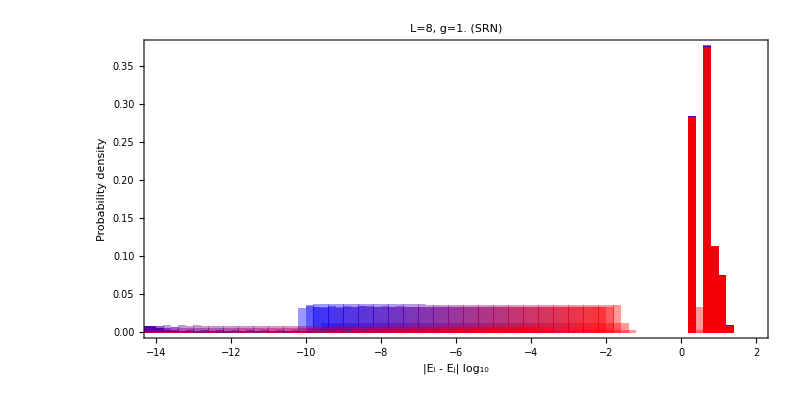

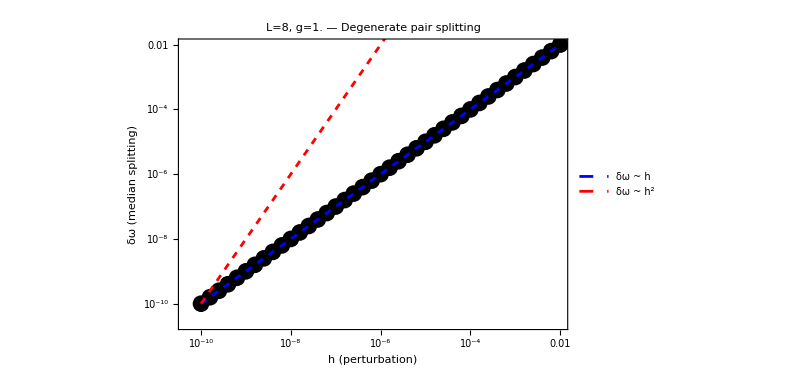

```mathematica
(* ================================================================*)
(*RUN:SRN example—fix g,scan h*)
(* ================================================================*)

Module[{LL=8,gVal=1.,JJ=1.,hScan,integSetup,integEVals,integOVals,allResults,plotData,splitData,medianSplits,logMin,logMax,colors,plt1,plt2},
(*Parameter scan*)
hScan=N[Table[10^x,{x,-10,-2,0.2}]];
(*Step 1:Diagonalize at integrability (h=0)*)
Print["Diagonalizing integrable limit (h=0)..."];
integSetup=setupForHG[0.,gVal,LL];
integEVals=integSetup["eVals"];
integOVals=integSetup["oVals"];
Print["  Even sector: ",Length[integEVals]," levels, ",Count[sectorGaps[integEVals],x_/;x<1.*^-10]," degenerate pairs"];
Print["  Odd sector:  ",Length[integOVals]," levels, ",Count[sectorGaps[integOVals],x_/;x<1.*^-10]," degenerate pairs"];
(*Step 2:Scan perturbation strengths*)allResults=Table[Module[{setup,eVals,oVals,eAll,eSplit,oAll,oSplit,nDegE,nDegO},Print["  h = ",hScan[[ih]],"..."];
setup=setupForHG[hScan[[ih]],gVal,LL];
eVals=setup["eVals"];oVals=setup["oVals"];
{eAll,eSplit,nDegE}=gapSplittingAnalysis[integEVals,eVals];
{oAll,oSplit,nDegO}=gapSplittingAnalysis[integOVals,oVals];
<|"h"->hScan[[ih]],"allGaps"->Join[eAll,oAll],"degSplittings"->Join[eSplit,oSplit],"nDegPairs"->nDegE+nDegO,"medianSplit"->If[Length[Join[eSplit,oSplit]]>0,Median[Select[Join[eSplit,oSplit],#>1.*^-14&]],0.]|>],{ih,Length[hScan]}];

(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)

logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (SRN)",14,Bold],ImageSize->800,AspectRatio->0.5];

(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)(* ============================================================*)

splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=Show[ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65],(*Overlay reference lines*)LogLogPlot[{medianSplits[[1,2]] (x/medianSplits[[1,1]])^1,medianSplits[[1,2]] (x/medianSplits[[1,1]])^2},{x,Min[hScan],Max[hScan]},PlotStyle->{{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["δω ~ h",12,Blue],Style["δω ~ \!\(\*SuperscriptBox[\(h\), \(2\)]\)",12,Red]},{0.75,0.3}]]];
Print[plt1];
Print[plt2];
(*Store for further use*)
$gapData=allResults;]
```

Diagonalizing integrable limit (h=0)...

Spectrum error: 3.55×10^-15 [OK]

Even sector: 136 levels, 804 degenerate pairs

Odd sector:  120 levels, 652 degenerate pairs

h = 1.×10^-10...

Spectrum error: 5.51×10^-14 [OK]

h = 1.58489×10^-10...

Spectrum error: 4.8×10^-14 [OK]

h = 2.51189×10^-10...

Spectrum error: 6.75×10^-14 [OK]

h = 3.98107×10^-10...

Spectrum error: 4.26×10^-14 [OK]

h = 6.30957×10^-10...

Spectrum error: 5.33×10^-14 [OK]

h = 1.×10^-9...

Spectrum error: 4.26×10^-14 [OK]

h = 1.58489×10^-9...

Spectrum error: 6.04×10^-14 [OK]

h = 2.51189×10^-9...

Spectrum error: 8.53×10^-14 [OK]

h = 3.98107×10^-9...

Spectrum error: 4.35×10^-14 [OK]

h = 6.30957×10^-9...

Spectrum error: 6.39×10^-14 [OK]

h = 1.×10^-8...

Spectrum error: 3.38×10^-14 [OK]

h = 1.58489×10^-8...

Spectrum error: 4.62×10^-14 [OK]

h = 2.51189×10^-8...

Spectrum error: 3.73×10^-14 [OK]

h = 3.98107×10^-8...

Spectrum error: 4.44×10^-14 [OK]

h = 6.30957×10^-8...

Spectrum error: 4.97×10^-14 [OK]

h = 1.×10^-7...

Spectrum error: 7.11×10^-14 [OK]

h = 1.58489×10^-7...

Spectrum error: 9.59×10^-14 [OK]

h = 2.51189×10^-7...

Spectrum error: 5.86×10^-14 [OK]

h = 3.98107×10^-7...

Spectrum error: 4.26×10^-14 [OK]

h = 6.30957×10^-7...

Spectrum error: 4.97×10^-14 [OK]

h = 1.×10^-6...

Spectrum error: 7.11×10^-14 [OK]

h = 1.58489×10^-6...

Spectrum error: 5.51×10^-14 [OK]

h = 2.51189×10^-6...

Spectrum error: 4.62×10^-14 [OK]

h = 3.98107×10^-6...

Spectrum error: 4.8×10^-14 [OK]

h = 6.30957×10^-6...

Spectrum error: 7.11×10^-14 [OK]

h = 0.00001...

Spectrum error: 5.15×10^-14 [OK]

h = 0.0000158489...

Spectrum error: 6.39×10^-14 [OK]

h = 0.0000251189...

Spectrum error: 6.57×10^-14 [OK]

h = 0.0000398107...

Spectrum error: 7.82×10^-14 [OK]

h = 0.0000630957...

Spectrum error: 8.53×10^-14 [OK]

h = 0.0001...

Spectrum error: 1.07×10^-13 [OK]

h = 0.000158489...

Spectrum error: 8.88×10^-14 [OK]

h = 0.000251189...

Spectrum error: 5.68×10^-14 [OK]

h = 0.000398107...

Spectrum error: 1.14×10^-13 [OK]

h = 0.000630957...

Spectrum error: 6.39×10^-14 [OK]

h = 0.001...

Spectrum error: 6.39×10^-14 [OK]

h = 0.00158489...

Spectrum error: 6.39×10^-14 [OK]

h = 0.00251189...

Spectrum error: 6.39×10^-14 [OK]

h = 0.00398107...

Spectrum error: 6.39×10^-14 [OK]

h = 0.00630957...

Spectrum error: 8.7×10^-14 [OK]

h = 0.01...

Spectrum error: 7.99×10^-14 [OK]

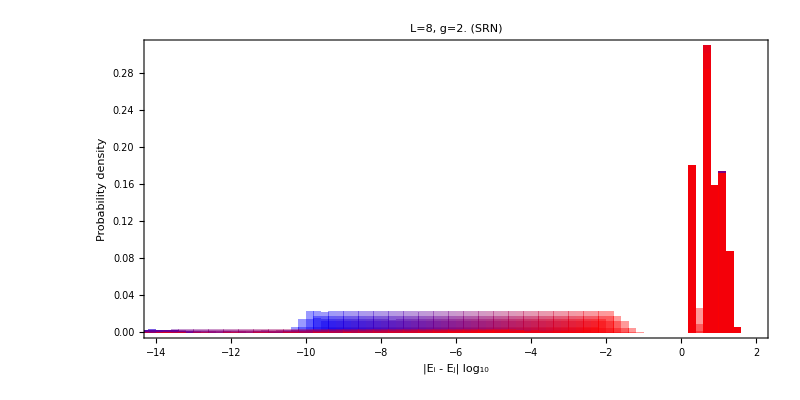

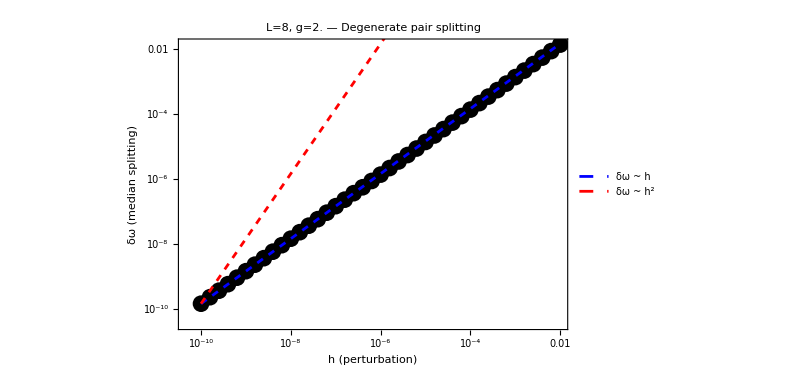

```mathematica
(* ================================================================*)
(*RUN:SRN example—fix g,scan h*)
(* ================================================================*)

Module[{LL=8,gVal=2.,JJ=1.,hScan,integSetup,integEVals,integOVals,allResults,plotData,splitData,medianSplits,logMin,logMax,colors,plt1,plt2},
(*Parameter scan*)
hScan=N[Table[10^x,{x,-10,-2,0.2}]];
(*Step 1:Diagonalize at integrability (h=0)*)
Print["Diagonalizing integrable limit (h=0)..."];
integSetup=setupForHG[0.,gVal,LL];
integEVals=integSetup["eVals"];
integOVals=integSetup["oVals"];
Print["  Even sector: ",Length[integEVals]," levels, ",Count[sectorGaps[integEVals],x_/;x<1.*^-10]," degenerate pairs"];
Print["  Odd sector:  ",Length[integOVals]," levels, ",Count[sectorGaps[integOVals],x_/;x<1.*^-10]," degenerate pairs"];
(*Step 2:Scan perturbation strengths*)allResults=Table[Module[{setup,eVals,oVals,eAll,eSplit,oAll,oSplit,nDegE,nDegO},Print["  h = ",hScan[[ih]],"..."];
setup=setupForHG[hScan[[ih]],gVal,LL];
eVals=setup["eVals"];oVals=setup["oVals"];
{eAll,eSplit,nDegE}=gapSplittingAnalysis[integEVals,eVals];
{oAll,oSplit,nDegO}=gapSplittingAnalysis[integOVals,oVals];
<|"h"->hScan[[ih]],"allGaps"->Join[eAll,oAll],"degSplittings"->Join[eSplit,oSplit],"nDegPairs"->nDegE+nDegO,"medianSplit"->If[Length[Join[eSplit,oSplit]]>0,Median[Select[Join[eSplit,oSplit],#>1.*^-14&]],0.]|>],{ih,Length[hScan]}];

(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)

logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (SRN)",14,Bold],ImageSize->800,AspectRatio->0.5];

(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)(* ============================================================*)

splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=Show[ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65],(*Overlay reference lines*)LogLogPlot[{medianSplits[[1,2]] (x/medianSplits[[1,1]])^1,medianSplits[[1,2]] (x/medianSplits[[1,1]])^2},{x,Min[hScan],Max[hScan]},PlotStyle->{{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["δω ~ h",12,Blue],Style["δω ~ \!\(\*SuperscriptBox[\(h\), \(2\)]\)",12,Red]},{0.75,0.3}]]];
Print[plt1];
Print[plt2];
(*Store for further use*)
$gapData=allResults;]
```

Diagonalizing integrable limit (h=0)...

Spectrum error: 1.78×10^-15 [OK]

Even sector: 136 levels, 821 degenerate pairs

Odd sector:  120 levels, 662 degenerate pairs

h = 1.×10^-10...

Spectrum error: 1.6×10^-14 [OK]

h = 1.58489×10^-10...

Spectrum error: 2.31×10^-14 [OK]

h = 2.51189×10^-10...

Spectrum error: 2.58×10^-14 [OK]

h = 3.98107×10^-10...

Spectrum error: 1.33×10^-14 [OK]

h = 6.30957×10^-10...

Spectrum error: 3.82×10^-14 [OK]

h = 1.×10^-9...

Spectrum error: 2.58×10^-14 [OK]

h = 1.58489×10^-9...

Spectrum error: 3.91×10^-14 [OK]

h = 2.51189×10^-9...

Spectrum error: 4.97×10^-14 [OK]

h = 3.98107×10^-9...

Spectrum error: 4.53×10^-14 [OK]

h = 6.30957×10^-9...

Spectrum error: 4.97×10^-14 [OK]

h = 1.×10^-8...

Spectrum error: 1.51×10^-14 [OK]

h = 1.58489×10^-8...

Spectrum error: 3.91×10^-14 [OK]

h = 2.51189×10^-8...

Spectrum error: 2.93×10^-14 [OK]

h = 3.98107×10^-8...

Spectrum error: 1.42×10^-14 [OK]

h = 6.30957×10^-8...

Spectrum error: 1.51×10^-14 [OK]

h = 1.×10^-7...

Spectrum error: 2.44×10^-14 [OK]

h = 1.58489×10^-7...

Spectrum error: 2.13×10^-14 [OK]

h = 2.51189×10^-7...

Spectrum error: 2.4×10^-14 [OK]

h = 3.98107×10^-7...

Spectrum error: 2.84×10^-14 [OK]

h = 6.30957×10^-7...

Spectrum error: 2.13×10^-14 [OK]

h = 1.×10^-6...

Spectrum error: 3.55×10^-14 [OK]

h = 1.58489×10^-6...

Spectrum error: 3.02×10^-14 [OK]

h = 2.51189×10^-6...

Spectrum error: 3.2×10^-14 [OK]

h = 3.98107×10^-6...

Spectrum error: 3.55×10^-14 [OK]

h = 6.30957×10^-6...

Spectrum error: 2.58×10^-14 [OK]

h = 0.00001...

Spectrum error: 3.55×10^-14 [OK]

h = 0.0000158489...

Spectrum error: 5.33×10^-14 [OK]

h = 0.0000251189...

Spectrum error: 3.2×10^-14 [OK]

h = 0.0000398107...

Spectrum error: 3.29×10^-14 [OK]

h = 0.0000630957...

Spectrum error: 1.95×10^-14 [OK]

h = 0.0001...

Spectrum error: 3.2×10^-14 [OK]

h = 0.000158489...

Spectrum error: 2.49×10^-14 [OK]

h = 0.000251189...

Spectrum error: 3.73×10^-14 [OK]

h = 0.000398107...

Spectrum error: 3.46×10^-14 [OK]

h = 0.000630957...

Spectrum error: 2.04×10^-14 [OK]

h = 0.001...

Spectrum error: 2.58×10^-14 [OK]

h = 0.00158489...

Spectrum error: 3.38×10^-14 [OK]

h = 0.00251189...

Spectrum error: 4.17×10^-14 [OK]

h = 0.00398107...

Spectrum error: 2.84×10^-14 [OK]

h = 0.00630957...

Spectrum error: 3.73×10^-14 [OK]

h = 0.01...

Spectrum error: 4.97×10^-14 [OK]

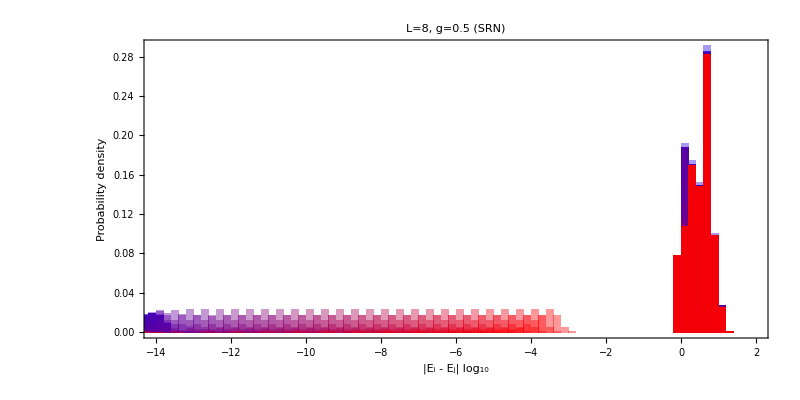

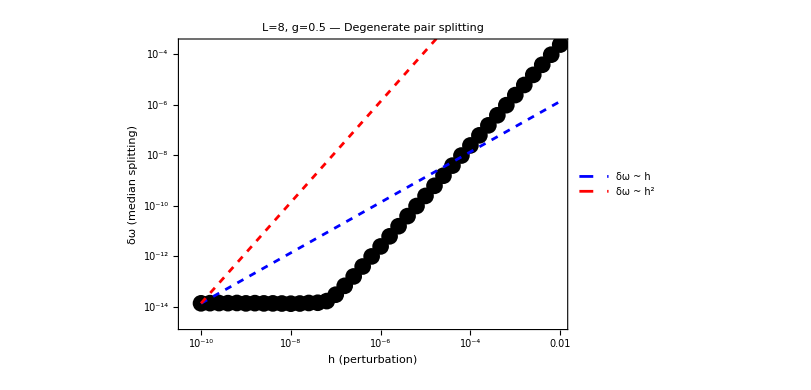

```mathematica
(* ================================================================*)
(*RUN:SRN example—fix g,scan h*)
(* ================================================================*)

Module[{LL=8,gVal=0.5,JJ=1.,hScan,integSetup,integEVals,integOVals,allResults,plotData,splitData,medianSplits,logMin,logMax,colors,plt1,plt2},
(*Parameter scan*)
hScan=N[Table[10^x,{x,-10,-2,0.2}]];
(*Step 1:Diagonalize at integrability (h=0)*)
Print["Diagonalizing integrable limit (h=0)..."];
integSetup=setupForHG[0.,gVal,LL];
integEVals=integSetup["eVals"];
integOVals=integSetup["oVals"];
Print["  Even sector: ",Length[integEVals]," levels, ",Count[sectorGaps[integEVals],x_/;x<1.*^-10]," degenerate pairs"];
Print["  Odd sector:  ",Length[integOVals]," levels, ",Count[sectorGaps[integOVals],x_/;x<1.*^-10]," degenerate pairs"];
(*Step 2:Scan perturbation strengths*)allResults=Table[Module[{setup,eVals,oVals,eAll,eSplit,oAll,oSplit,nDegE,nDegO},Print["  h = ",hScan[[ih]],"..."];
setup=setupForHG[hScan[[ih]],gVal,LL];
eVals=setup["eVals"];oVals=setup["oVals"];
{eAll,eSplit,nDegE}=gapSplittingAnalysis[integEVals,eVals];
{oAll,oSplit,nDegO}=gapSplittingAnalysis[integOVals,oVals];
<|"h"->hScan[[ih]],"allGaps"->Join[eAll,oAll],"degSplittings"->Join[eSplit,oSplit],"nDegPairs"->nDegE+nDegO,"medianSplit"->If[Length[Join[eSplit,oSplit]]>0,Median[Select[Join[eSplit,oSplit],#>1.*^-14&]],0.]|>],{ih,Length[hScan]}];

(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)

logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (SRN)",14,Bold],ImageSize->800,AspectRatio->0.5];

(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)(* ============================================================*)

splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=Show[ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65],(*Overlay reference lines*)LogLogPlot[{medianSplits[[1,2]] (x/medianSplits[[1,1]])^1,medianSplits[[1,2]] (x/medianSplits[[1,1]])^2},{x,Min[hScan],Max[hScan]},PlotStyle->{{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["δω ~ h",12,Blue],Style["δω ~ \!\(\*SuperscriptBox[\(h\), \(2\)]\)",12,Red]},{0.75,0.3}]]];
Print[plt1];
Print[plt2];
(*Store for further use*)
$gapData=allResults;]
```

Diagonalizing integrable limit (h=0)...

Spectrum error: 3.55×10^-15 [OK]

Even sector: 136 levels, 347 degenerate pairs

Odd sector:  120 levels, 292 degenerate pairs

h = 1.×10^-10...

Spectrum error: 3.89×10^-14 [OK]

h = 1.58489×10^-10...

Spectrum error: 5.6×10^-14 [OK]

h = 2.51189×10^-10...

Spectrum error: 7.28×10^-14 [OK]

h = 3.98107×10^-10...

Spectrum error: 5.68×10^-14 [OK]

h = 6.30957×10^-10...

Spectrum error: 5.86×10^-14 [OK]

h = 1.×10^-9...

Spectrum error: 3.73×10^-14 [OK]

h = 1.58489×10^-9...

Spectrum error: 4.09×10^-14 [OK]

h = 2.51189×10^-9...

Spectrum error: 3.02×10^-14 [OK]

h = 3.98107×10^-9...

Spectrum error: 3.55×10^-14 [OK]

h = 6.30957×10^-9...

Spectrum error: 3.73×10^-14 [OK]

h = 1.×10^-8...

Spectrum error: 4.8×10^-14 [OK]

h = 1.58489×10^-8...

Spectrum error: 3.55×10^-14 [OK]

h = 2.51189×10^-8...

Spectrum error: 4.8×10^-14 [OK]

h = 3.98107×10^-8...

Spectrum error: 3.55×10^-14 [OK]

h = 6.30957×10^-8...

Spectrum error: 2.84×10^-14 [OK]

h = 1.×10^-7...

Spectrum error: 3.55×10^-14 [OK]

h = 1.58489×10^-7...

Spectrum error: 6.39×10^-14 [OK]

h = 2.51189×10^-7...

Spectrum error: 3.55×10^-14 [OK]

h = 3.98107×10^-7...

Spectrum error: 4.44×10^-14 [OK]

h = 6.30957×10^-7...

Spectrum error: 6.22×10^-14 [OK]

h = 1.×10^-6...

Spectrum error: 4.62×10^-14 [OK]

h = 1.58489×10^-6...

Spectrum error: 8.88×10^-14 [OK]

h = 2.51189×10^-6...

Spectrum error: 5.15×10^-14 [OK]

h = 3.98107×10^-6...

Spectrum error: 4.44×10^-14 [OK]

h = 6.30957×10^-6...

Spectrum error: 7.11×10^-14 [OK]

h = 0.00001...

Spectrum error: 5.51×10^-14 [OK]

h = 0.0000158489...

Spectrum error: 6.39×10^-14 [OK]

h = 0.0000251189...

Spectrum error: 6.04×10^-14 [OK]

h = 0.0000398107...

Spectrum error: 5.15×10^-14 [OK]

h = 0.0000630957...

Spectrum error: 5.51×10^-14 [OK]

h = 0.0001...

Spectrum error: 4.97×10^-14 [OK]

h = 0.000158489...

Spectrum error: 5.51×10^-14 [OK]

h = 0.000251189...

Spectrum error: 6.93×10^-14 [OK]

h = 0.000398107...

Spectrum error: 6.75×10^-14 [OK]

h = 0.000630957...

Spectrum error: 4.26×10^-14 [OK]

h = 0.001...

Spectrum error: 4.09×10^-14 [OK]

h = 0.00158489...

Spectrum error: 7.82×10^-14 [OK]

h = 0.00251189...

Spectrum error: 5.33×10^-14 [OK]

h = 0.00398107...

Spectrum error: 6.39×10^-14 [OK]

h = 0.00630957...

Spectrum error: 5.68×10^-14 [OK]

h = 0.01...

Spectrum error: 4.44×10^-14 [OK]

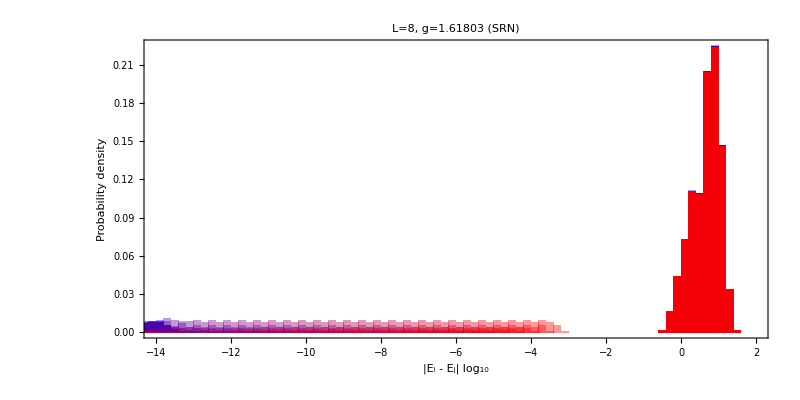

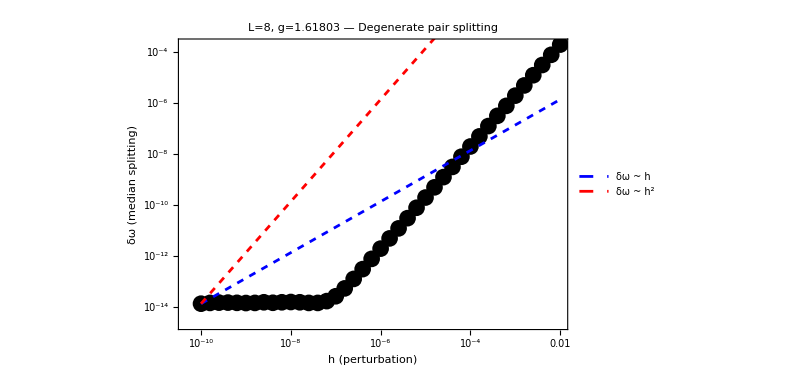

```mathematica
(* ================================================================*)
(*RUN:SRN example—fix g,scan h*)
(* ================================================================*)

Module[{LL=8,gVal=N[GoldenRatio],JJ=1.,hScan,integSetup,integEVals,integOVals,allResults,plotData,splitData,medianSplits,logMin,logMax,colors,plt1,plt2},
(*Parameter scan*)
hScan=N[Table[10^x,{x,-10,-2,0.2}]];
(*Step 1:Diagonalize at integrability (h=0)*)
Print["Diagonalizing integrable limit (h=0)..."];
integSetup=setupForHG[0.,gVal,LL];
integEVals=integSetup["eVals"];
integOVals=integSetup["oVals"];
Print["  Even sector: ",Length[integEVals]," levels, ",Count[sectorGaps[integEVals],x_/;x<1.*^-10]," degenerate pairs"];
Print["  Odd sector:  ",Length[integOVals]," levels, ",Count[sectorGaps[integOVals],x_/;x<1.*^-10]," degenerate pairs"];
(*Step 2:Scan perturbation strengths*)allResults=Table[Module[{setup,eVals,oVals,eAll,eSplit,oAll,oSplit,nDegE,nDegO},Print["  h = ",hScan[[ih]],"..."];
setup=setupForHG[hScan[[ih]],gVal,LL];
eVals=setup["eVals"];oVals=setup["oVals"];
{eAll,eSplit,nDegE}=gapSplittingAnalysis[integEVals,eVals];
{oAll,oSplit,nDegO}=gapSplittingAnalysis[integOVals,oVals];
<|"h"->hScan[[ih]],"allGaps"->Join[eAll,oAll],"degSplittings"->Join[eSplit,oSplit],"nDegPairs"->nDegE+nDegO,"medianSplit"->If[Length[Join[eSplit,oSplit]]>0,Median[Select[Join[eSplit,oSplit],#>1.*^-14&]],0.]|>],{ih,Length[hScan]}];

(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)

logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (SRN)",14,Bold],ImageSize->800,AspectRatio->0.5];

(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)(* ============================================================*)

splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=Show[ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65],(*Overlay reference lines*)LogLogPlot[{medianSplits[[1,2]] (x/medianSplits[[1,1]])^1,medianSplits[[1,2]] (x/medianSplits[[1,1]])^2},{x,Min[hScan],Max[hScan]},PlotStyle->{{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["δω ~ h",12,Blue],Style["δω ~ \!\(\*SuperscriptBox[\(h\), \(2\)]\)",12,Red]},{0.75,0.3}]]];
Print[plt1];
Print[plt2];
(*Store for further use*)
$gapData=allResults;]
```

Diagonalizing integrable limit (h=0)...

Spectrum error: 1.78×10^-15 [OK]

Even sector: 136 levels, 347 degenerate pairs

Odd sector:  120 levels, 292 degenerate pairs

h = 1.×10^-10...

Spectrum error: 6.39×10^-14 [OK]

h = 1.58489×10^-10...

Spectrum error: 4.44×10^-14 [OK]

h = 2.51189×10^-10...

Spectrum error: 2.31×10^-14 [OK]

h = 3.98107×10^-10...

Spectrum error: 3.38×10^-14 [OK]

h = 6.30957×10^-10...

Spectrum error: 3.2×10^-14 [OK]

h = 1.×10^-9...

Spectrum error: 3.46×10^-14 [OK]

h = 1.58489×10^-9...

Spectrum error: 1.78×10^-14 [OK]

h = 2.51189×10^-9...

Spectrum error: 2.13×10^-14 [OK]

h = 3.98107×10^-9...

Spectrum error: 2.49×10^-14 [OK]

h = 6.30957×10^-9...

Spectrum error: 2.18×10^-14 [OK]

h = 1.×10^-8...

Spectrum error: 4.26×10^-14 [OK]

h = 1.58489×10^-8...

Spectrum error: 2.58×10^-14 [OK]

h = 2.51189×10^-8...

Spectrum error: 3.55×10^-14 [OK]

h = 3.98107×10^-8...

Spectrum error: 2.84×10^-14 [OK]

h = 6.30957×10^-8...

Spectrum error: 2.13×10^-14 [OK]

h = 1.×10^-7...

Spectrum error: 2.49×10^-14 [OK]

h = 1.58489×10^-7...

Spectrum error: 2.75×10^-14 [OK]

h = 2.51189×10^-7...

Spectrum error: 3.73×10^-14 [OK]

h = 3.98107×10^-7...

Spectrum error: 4.×10^-14 [OK]

h = 6.30957×10^-7...

Spectrum error: 3.46×10^-14 [OK]

h = 1.×10^-6...

Spectrum error: 4.62×10^-14 [OK]

h = 1.58489×10^-6...

Spectrum error: 5.51×10^-14 [OK]

h = 2.51189×10^-6...

Spectrum error: 4.44×10^-14 [OK]

h = 3.98107×10^-6...

Spectrum error: 3.02×10^-14 [OK]

h = 6.30957×10^-6...

Spectrum error: 2.22×10^-14 [OK]

h = 0.00001...

Spectrum error: 3.02×10^-14 [OK]

h = 0.0000158489...

Spectrum error: 2.93×10^-14 [OK]

h = 0.0000251189...

Spectrum error: 3.55×10^-14 [OK]

h = 0.0000398107...

Spectrum error: 2.13×10^-14 [OK]

h = 0.0000630957...

Spectrum error: 3.55×10^-14 [OK]

h = 0.0001...

Spectrum error: 2.66×10^-14 [OK]

h = 0.000158489...

Spectrum error: 1.95×10^-14 [OK]

h = 0.000251189...

Spectrum error: 2.13×10^-14 [OK]

h = 0.000398107...

Spectrum error: 5.06×10^-14 [OK]

h = 0.000630957...

Spectrum error: 2.75×10^-14 [OK]

h = 0.001...

Spectrum error: 3.55×10^-14 [OK]

h = 0.00158489...

Spectrum error: 3.02×10^-14 [OK]

h = 0.00251189...

Spectrum error: 3.38×10^-14 [OK]

h = 0.00398107...

Spectrum error: 3.29×10^-14 [OK]

h = 0.00630957...

Spectrum error: 3.29×10^-14 [OK]

h = 0.01...

Spectrum error: 2.93×10^-14 [OK]

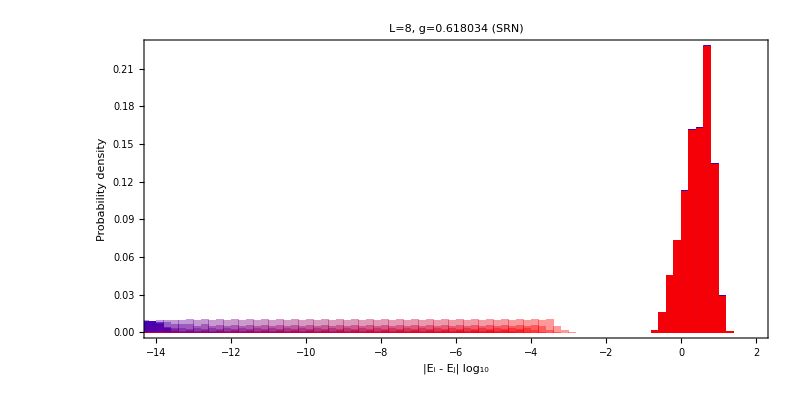

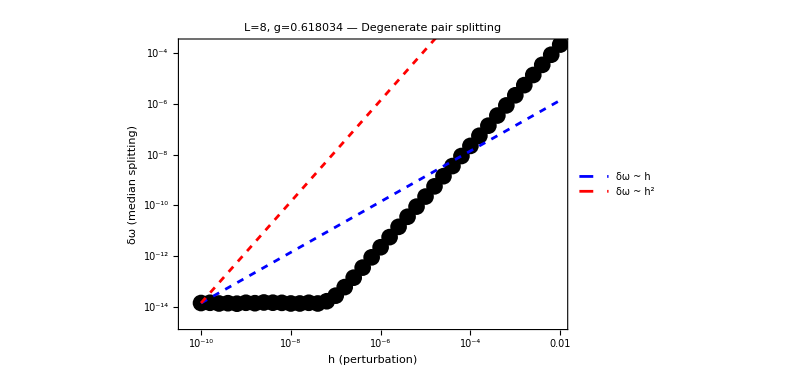

```mathematica
(* ================================================================*)
(*RUN:SRN example—fix g,scan h*)
(* ================================================================*)

Module[{LL=8,gVal=N[1/GoldenRatio],JJ=1.,hScan,integSetup,integEVals,integOVals,allResults,plotData,splitData,medianSplits,logMin,logMax,colors,plt1,plt2},
(*Parameter scan*)
hScan=N[Table[10^x,{x,-10,-2,0.2}]];
(*Step 1:Diagonalize at integrability (h=0)*)
Print["Diagonalizing integrable limit (h=0)..."];
integSetup=setupForHG[0.,gVal,LL];
integEVals=integSetup["eVals"];
integOVals=integSetup["oVals"];
Print["  Even sector: ",Length[integEVals]," levels, ",Count[sectorGaps[integEVals],x_/;x<1.*^-10]," degenerate pairs"];
Print["  Odd sector:  ",Length[integOVals]," levels, ",Count[sectorGaps[integOVals],x_/;x<1.*^-10]," degenerate pairs"];
(*Step 2:Scan perturbation strengths*)allResults=Table[Module[{setup,eVals,oVals,eAll,eSplit,oAll,oSplit,nDegE,nDegO},Print["  h = ",hScan[[ih]],"..."];
setup=setupForHG[hScan[[ih]],gVal,LL];
eVals=setup["eVals"];oVals=setup["oVals"];
{eAll,eSplit,nDegE}=gapSplittingAnalysis[integEVals,eVals];
{oAll,oSplit,nDegO}=gapSplittingAnalysis[integOVals,oVals];
<|"h"->hScan[[ih]],"allGaps"->Join[eAll,oAll],"degSplittings"->Join[eSplit,oSplit],"nDegPairs"->nDegE+nDegO,"medianSplit"->If[Length[Join[eSplit,oSplit]]>0,Median[Select[Join[eSplit,oSplit],#>1.*^-14&]],0.]|>],{ih,Length[hScan]}];

(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)

logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (SRN)",14,Bold],ImageSize->800,AspectRatio->0.5];

(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)(* ============================================================*)

splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=Show[ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65],(*Overlay reference lines*)LogLogPlot[{medianSplits[[1,2]] (x/medianSplits[[1,1]])^1,medianSplits[[1,2]] (x/medianSplits[[1,1]])^2},{x,Min[hScan],Max[hScan]},PlotStyle->{{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["δω ~ h",12,Blue],Style["δω ~ \!\(\*SuperscriptBox[\(h\), \(2\)]\)",12,Red]},{0.75,0.3}]]];
Print[plt1];
Print[plt2];
(*Store for further use*)
$gapData=allResults;]
```

Diagonalizing integrable limit (h=0)...

Spectrum error: 3.55×10^-15 [OK]

Even sector: 136 levels, 359 degenerate pairs

Odd sector:  120 levels, 300 degenerate pairs

h = 1.×10^-10...

Spectrum error: 8.88×10^-14 [OK]

h = 1.58489×10^-10...

Spectrum error: 6.22×10^-14 [OK]

h = 2.51189×10^-10...

Spectrum error: 7.28×10^-14 [OK]

h = 3.98107×10^-10...

Spectrum error: 6.57×10^-14 [OK]

h = 6.30957×10^-10...

Spectrum error: 6.93×10^-14 [OK]

h = 1.×10^-9...

Spectrum error: 7.11×10^-14 [OK]

h = 1.58489×10^-9...

Spectrum error: 6.93×10^-14 [OK]

h = 2.51189×10^-9...

Spectrum error: 8.17×10^-14 [OK]

h = 3.98107×10^-9...

Spectrum error: 8.53×10^-14 [OK]

h = 6.30957×10^-9...

Spectrum error: 7.46×10^-14 [OK]

h = 1.×10^-8...

Spectrum error: 7.11×10^-14 [OK]

h = 1.58489×10^-8...

Spectrum error: 6.48×10^-14 [OK]

h = 2.51189×10^-8...

Spectrum error: 5.68×10^-14 [OK]

h = 3.98107×10^-8...

Spectrum error: 7.11×10^-14 [OK]

h = 6.30957×10^-8...

Spectrum error: 8.17×10^-14 [OK]

h = 1.×10^-7...

Spectrum error: 5.68×10^-14 [OK]

h = 1.58489×10^-7...

Spectrum error: 6.39×10^-14 [OK]

h = 2.51189×10^-7...

Spectrum error: 6.93×10^-14 [OK]

h = 3.98107×10^-7...

Spectrum error: 7.82×10^-14 [OK]

h = 6.30957×10^-7...

Spectrum error: 6.57×10^-14 [OK]

h = 1.×10^-6...

Spectrum error: 5.68×10^-14 [OK]

h = 1.58489×10^-6...

Spectrum error: 8.17×10^-14 [OK]

h = 2.51189×10^-6...

Spectrum error: 8.53×10^-14 [OK]

h = 3.98107×10^-6...

Spectrum error: 8.17×10^-14 [OK]

h = 6.30957×10^-6...

Spectrum error: 7.82×10^-14 [OK]

h = 0.00001...

Spectrum error: 9.24×10^-14 [OK]

h = 0.0000158489...

Spectrum error: 8.35×10^-14 [OK]

h = 0.0000251189...

Spectrum error: 8.17×10^-14 [OK]

h = 0.0000398107...

Spectrum error: 5.68×10^-14 [OK]

h = 0.0000630957...

Spectrum error: 7.64×10^-14 [OK]

h = 0.0001...

Spectrum error: 6.04×10^-14 [OK]

h = 0.000158489...

Spectrum error: 7.46×10^-14 [OK]

h = 0.000251189...

Spectrum error: 6.39×10^-14 [OK]

h = 0.000398107...

Spectrum error: 4.97×10^-14 [OK]

h = 0.000630957...

Spectrum error: 9.24×10^-14 [OK]

h = 0.001...

Spectrum error: 9.95×10^-14 [OK]

h = 0.00158489...

Spectrum error: 7.11×10^-14 [OK]

h = 0.00251189...

Spectrum error: 8.17×10^-14 [OK]

h = 0.00398107...

Spectrum error: 6.75×10^-14 [OK]

h = 0.00630957...

Spectrum error: 6.22×10^-14 [OK]

h = 0.01...

Spectrum error: 9.06×10^-14 [OK]

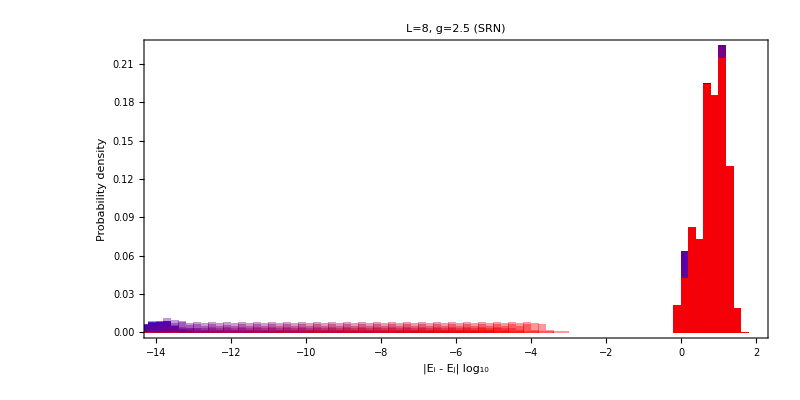

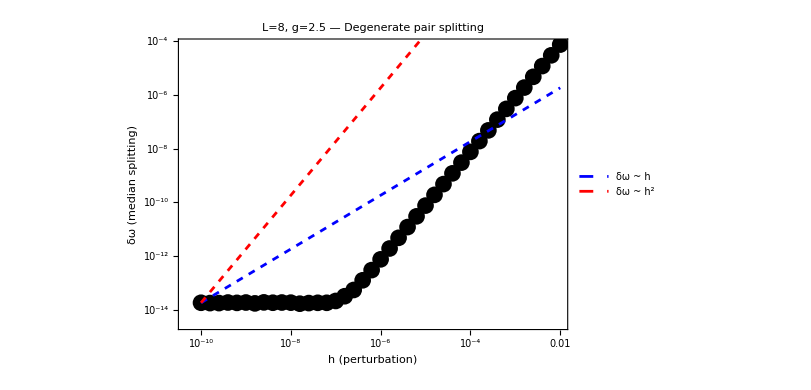

```mathematica
(* ================================================================*)
(*RUN:SRN example—fix g,scan h*)
(* ================================================================*)

Module[{LL=8,gVal=2.5,JJ=1.,hScan,integSetup,integEVals,integOVals,allResults,plotData,splitData,medianSplits,logMin,logMax,colors,plt1,plt2},
(*Parameter scan*)
hScan=N[Table[10^x,{x,-10,-2,0.2}]];
(*Step 1:Diagonalize at integrability (h=0)*)
Print["Diagonalizing integrable limit (h=0)..."];
integSetup=setupForHG[0.,gVal,LL];
integEVals=integSetup["eVals"];
integOVals=integSetup["oVals"];
Print["  Even sector: ",Length[integEVals]," levels, ",Count[sectorGaps[integEVals],x_/;x<1.*^-10]," degenerate pairs"];
Print["  Odd sector:  ",Length[integOVals]," levels, ",Count[sectorGaps[integOVals],x_/;x<1.*^-10]," degenerate pairs"];
(*Step 2:Scan perturbation strengths*)allResults=Table[Module[{setup,eVals,oVals,eAll,eSplit,oAll,oSplit,nDegE,nDegO},Print["  h = ",hScan[[ih]],"..."];
setup=setupForHG[hScan[[ih]],gVal,LL];
eVals=setup["eVals"];oVals=setup["oVals"];
{eAll,eSplit,nDegE}=gapSplittingAnalysis[integEVals,eVals];
{oAll,oSplit,nDegO}=gapSplittingAnalysis[integOVals,oVals];
<|"h"->hScan[[ih]],"allGaps"->Join[eAll,oAll],"degSplittings"->Join[eSplit,oSplit],"nDegPairs"->nDegE+nDegO,"medianSplit"->If[Length[Join[eSplit,oSplit]]>0,Median[Select[Join[eSplit,oSplit],#>1.*^-14&]],0.]|>],{ih,Length[hScan]}];

(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)

logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (SRN)",14,Bold],ImageSize->800,AspectRatio->0.5];

(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)(* ============================================================*)

splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=Show[ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65],(*Overlay reference lines*)LogLogPlot[{medianSplits[[1,2]] (x/medianSplits[[1,1]])^1,medianSplits[[1,2]] (x/medianSplits[[1,1]])^2},{x,Min[hScan],Max[hScan]},PlotStyle->{{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["δω ~ h",12,Blue],Style["δω ~ \!\(\*SuperscriptBox[\(h\), \(2\)]\)",12,Red]},{0.75,0.3}]]];
Print[plt1];
Print[plt2];
(*Store for further use*)
$gapData=allResults;]
```

Diagonalizing integrable limit (h=0)...

Spectrum error: 3.55×10^-15 [OK]

Even sector: 136 levels, 529 degenerate pairs

Odd sector:  120 levels, 428 degenerate pairs

h = 1.×10^-10...

Spectrum error: 7.46×10^-14 [OK]

h = 1.58489×10^-10...

Spectrum error: 9.06×10^-14 [OK]

h = 2.51189×10^-10...

Spectrum error: 7.82×10^-14 [OK]

h = 3.98107×10^-10...

Spectrum error: 5.33×10^-14 [OK]

h = 6.30957×10^-10...

Spectrum error: 1.14×10^-13 [OK]

h = 1.×10^-9...

Spectrum error: 9.59×10^-14 [OK]

h = 1.58489×10^-9...

Spectrum error: 7.46×10^-14 [OK]

h = 2.51189×10^-9...

Spectrum error: 6.75×10^-14 [OK]

h = 3.98107×10^-9...

Spectrum error: 8.17×10^-14 [OK]

h = 6.30957×10^-9...

Spectrum error: 8.53×10^-14 [OK]

h = 1.×10^-8...

Spectrum error: 8.53×10^-14 [OK]

h = 1.58489×10^-8...

Spectrum error: 1.35×10^-13 [OK]

h = 2.51189×10^-8...

Spectrum error: 7.11×10^-14 [OK]

h = 3.98107×10^-8...

Spectrum error: 1.03×10^-13 [OK]

h = 6.30957×10^-8...

Spectrum error: 9.95×10^-14 [OK]

h = 1.×10^-7...

Spectrum error: 6.75×10^-14 [OK]

h = 1.58489×10^-7...

Spectrum error: 9.24×10^-14 [OK]

h = 2.51189×10^-7...

Spectrum error: 6.22×10^-14 [OK]

h = 3.98107×10^-7...

Spectrum error: 4.26×10^-14 [OK]

h = 6.30957×10^-7...

Spectrum error: 8.53×10^-14 [OK]

h = 1.×10^-6...

Spectrum error: 9.59×10^-14 [OK]

h = 1.58489×10^-6...

Spectrum error: 4.8×10^-14 [OK]

h = 2.51189×10^-6...

Spectrum error: 7.46×10^-14 [OK]

h = 3.98107×10^-6...

Spectrum error: 1.78×10^-13 [OK]

h = 6.30957×10^-6...

Spectrum error: 7.11×10^-14 [OK]

h = 0.00001...

Spectrum error: 1.39×10^-13 [OK]

h = 0.0000158489...

Spectrum error: 6.75×10^-14 [OK]

h = 0.0000251189...

Spectrum error: 9.59×10^-14 [OK]

h = 0.0000398107...

Spectrum error: 1.07×10^-13 [OK]

h = 0.0000630957...

Spectrum error: 9.95×10^-14 [OK]

h = 0.0001...

Spectrum error: 1.53×10^-13 [OK]

h = 0.000158489...

Spectrum error: 7.82×10^-14 [OK]

h = 0.000251189...

Spectrum error: 9.24×10^-14 [OK]

h = 0.000398107...

Spectrum error: 8.53×10^-14 [OK]

h = 0.000630957...

Spectrum error: 6.04×10^-14 [OK]

h = 0.001...

Spectrum error: 7.82×10^-14 [OK]

h = 0.00158489...

Spectrum error: 9.59×10^-14 [OK]

h = 0.00251189...

Spectrum error: 8.88×10^-14 [OK]

h = 0.00398107...

Spectrum error: 6.04×10^-14 [OK]

h = 0.00630957...

Spectrum error: 1.03×10^-13 [OK]

h = 0.01...

Spectrum error: 9.59×10^-14 [OK]

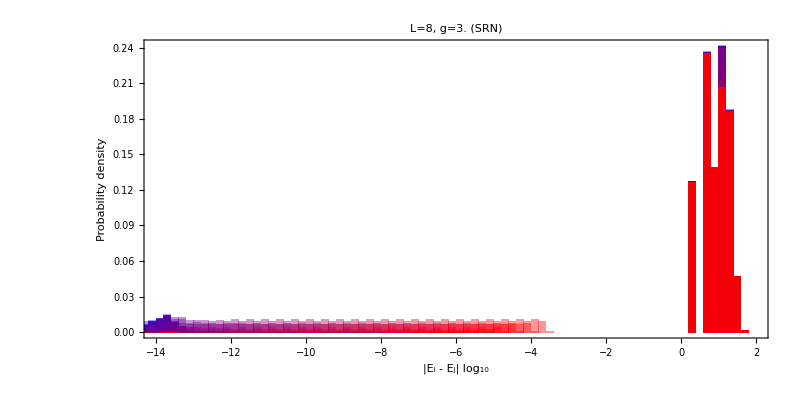

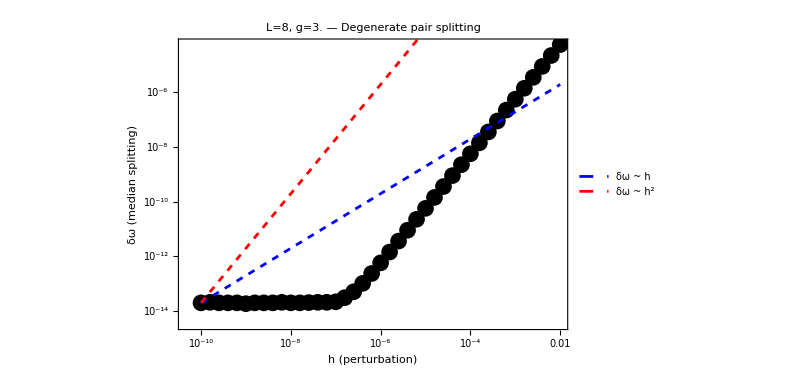

```mathematica
(* ================================================================*)
(*RUN:SRN example—fix g,scan h*)
(* ================================================================*)

Module[{LL=8,gVal=3.,JJ=1.,hScan,integSetup,integEVals,integOVals,allResults,plotData,splitData,medianSplits,logMin,logMax,colors,plt1,plt2},
(*Parameter scan*)
hScan=N[Table[10^x,{x,-10,-2,0.2}]];
(*Step 1:Diagonalize at integrability (h=0)*)
Print["Diagonalizing integrable limit (h=0)..."];
integSetup=setupForHG[0.,gVal,LL];
integEVals=integSetup["eVals"];
integOVals=integSetup["oVals"];
Print["  Even sector: ",Length[integEVals]," levels, ",Count[sectorGaps[integEVals],x_/;x<1.*^-10]," degenerate pairs"];
Print["  Odd sector:  ",Length[integOVals]," levels, ",Count[sectorGaps[integOVals],x_/;x<1.*^-10]," degenerate pairs"];
(*Step 2:Scan perturbation strengths*)allResults=Table[Module[{setup,eVals,oVals,eAll,eSplit,oAll,oSplit,nDegE,nDegO},Print["  h = ",hScan[[ih]],"..."];
setup=setupForHG[hScan[[ih]],gVal,LL];
eVals=setup["eVals"];oVals=setup["oVals"];
{eAll,eSplit,nDegE}=gapSplittingAnalysis[integEVals,eVals];
{oAll,oSplit,nDegO}=gapSplittingAnalysis[integOVals,oVals];
<|"h"->hScan[[ih]],"allGaps"->Join[eAll,oAll],"degSplittings"->Join[eSplit,oSplit],"nDegPairs"->nDegE+nDegO,"medianSplit"->If[Length[Join[eSplit,oSplit]]>0,Median[Select[Join[eSplit,oSplit],#>1.*^-14&]],0.]|>],{ih,Length[hScan]}];

(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)

logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (SRN)",14,Bold],ImageSize->800,AspectRatio->0.5];

(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)(* ============================================================*)

splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=Show[ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65],(*Overlay reference lines*)LogLogPlot[{medianSplits[[1,2]] (x/medianSplits[[1,1]])^1,medianSplits[[1,2]] (x/medianSplits[[1,1]])^2},{x,Min[hScan],Max[hScan]},PlotStyle->{{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["δω ~ h",12,Blue],Style["δω ~ \!\(\*SuperscriptBox[\(h\), \(2\)]\)",12,Red]},{0.75,0.3}]]];
Print[plt1];
Print[plt2];
(*Store for further use*)
$gapData=allResults;]
```

## LRN

```mathematica
(* ================================================================*)
(*RUN:SRN example—fix g,scan h*)
(* ================================================================*)

Module[{LL=8,gVal=1.,JJ=1.,hScan,integSetup,integEVals,integOVals,allResults,plotData,splitData,medianSplits,logMin,logMax,colors,plt1,plt2},
(*Parameter scan*)
hScan=N[Table[10^x,{x,-10,-2,0.2}]];
(*Step 1:Diagonalize at integrability (h=0)*)
Print["Diagonalizing integrable limit (h=0)..."];
integSetup=setupForHG[gVal,0.,LL];
integEVals=integSetup["eVals"];
integOVals=integSetup["oVals"];
Print["  Even sector: ",Length[integEVals]," levels, ",Count[sectorGaps[integEVals],x_/;x<1.*^-10]," degenerate pairs"];
Print["  Odd sector:  ",Length[integOVals]," levels, ",Count[sectorGaps[integOVals],x_/;x<1.*^-10]," degenerate pairs"];
(*Step 2:Scan perturbation strengths*)allResults=Table[Module[{setup,eVals,oVals,eAll,eSplit,oAll,oSplit,nDegE,nDegO},Print["  h = ",hScan[[ih]],"..."];
setup=setupForHG[hScan[[ih]],gVal,LL];
eVals=setup["eVals"];oVals=setup["oVals"];
{eAll,eSplit,nDegE}=gapSplittingAnalysis[integEVals,eVals];
{oAll,oSplit,nDegO}=gapSplittingAnalysis[integOVals,oVals];
<|"h"->hScan[[ih]],"allGaps"->Join[eAll,oAll],"degSplittings"->Join[eSplit,oSplit],"nDegPairs"->nDegE+nDegO,"medianSplit"->If[Length[Join[eSplit,oSplit]]>0,Median[Select[Join[eSplit,oSplit],#>1.*^-14&]],0.]|>],{ih,Length[hScan]}];

(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)

logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (LRN)",14,Bold],ImageSize->800,AspectRatio->0.5];

(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)(* ============================================================*)

splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=Show[ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},PlotRange->All,Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65],(*Overlay reference lines*)LogLogPlot[{medianSplits[[1,2]] (x/medianSplits[[1,1]])^1,medianSplits[[1,2]] (x/medianSplits[[1,1]])^2},{x,Min[hScan],Max[hScan]},PlotStyle->{{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["δω ~ h",12,Blue],Style["δω ~ \!\(\*SuperscriptBox[\(h\), \(2\)]\)",12,Red]},{0.75,0.3}]]];
Print[plt1];
Print[plt2];
(*Store for further use*)
$gapData=allResults;]
```

## TESTS

```mathematica
(* ================================================================*)
(*RUN:SRN example—fix g,scan h*)
(* ================================================================*)

LL=8;
gVal=1.;
JJ=1.;
(*Parameter scan*)
hScan=N[Table[10^x,{x,-8,-1,0.1}]];
```

```mathematica
(*Step 1:Diagonalize at integrability (h=0)*)
Print["Diagonalizing integrable limit (h=0)..."];
integSetup=setupForHG[0.,gVal,LL];
integEVals=integSetup["eVals"];
integOVals=integSetup["oVals"];
Print["  Even sector: ",Length[integEVals]," levels, ",Count[sectorGaps[integEVals],x_/;x<1.*^-10]," degenerate pairs"];
Print["  Odd sector:  ",Length[integOVals]," levels, ",Count[sectorGaps[integOVals],x_/;x<1.*^-10]," degenerate pairs"];
(*Step 2:Scan perturbation strengths*)
allResults=Table[
Module[{setup,eVals,oVals,eAll,eSplit,oAll,oSplit,nDegE,nDegO},Print["  h = ",hScan[[ih]],"..."];
setup=setupForHG[gVal,hScan[[ih]],LL];
eVals=setup["eVals"];
oVals=setup["oVals"];
{eAll,eSplit,nDegE}=gapSplittingAnalysis[integEVals,eVals];
{oAll,oSplit,nDegO}=gapSplittingAnalysis[integOVals,oVals];
<|"h"->hScan[[ih]],"allGaps"->Join[eAll,oAll],"degSplittings"->Join[eSplit,oSplit],"nDegPairs"->nDegE+nDegO,"medianSplit"->If[Length[Join[eSplit,oSplit]]>0,Median[Select[Join[eSplit,oSplit],#>1.*^-14&]],0.]|>]
,{ih,Length[hScan]}];
```

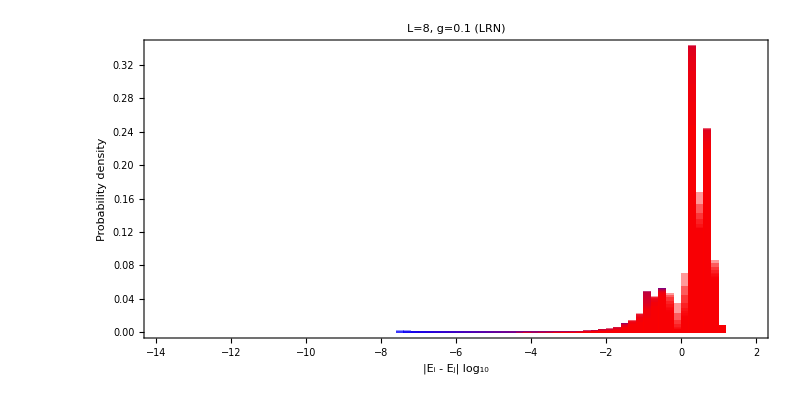

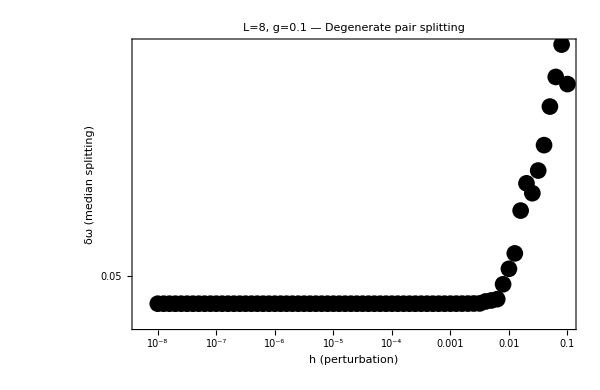

```mathematica
(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)
logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (LRN)",14,Bold],ImageSize->800,AspectRatio->0.5]
(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)
splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65]
```

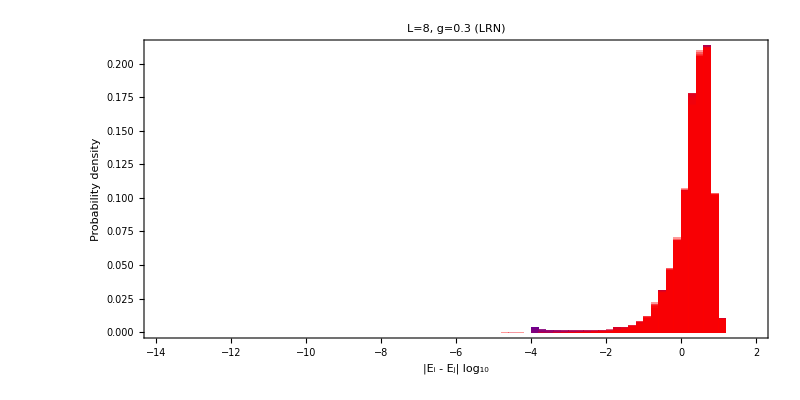

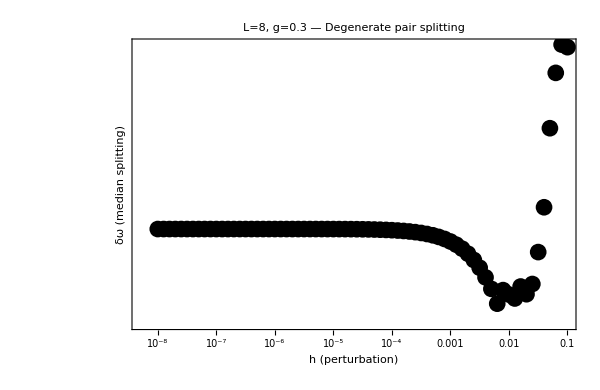

```mathematica
(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)
logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (LRN)",14,Bold],ImageSize->800,AspectRatio->0.5]
(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)
splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65]
```

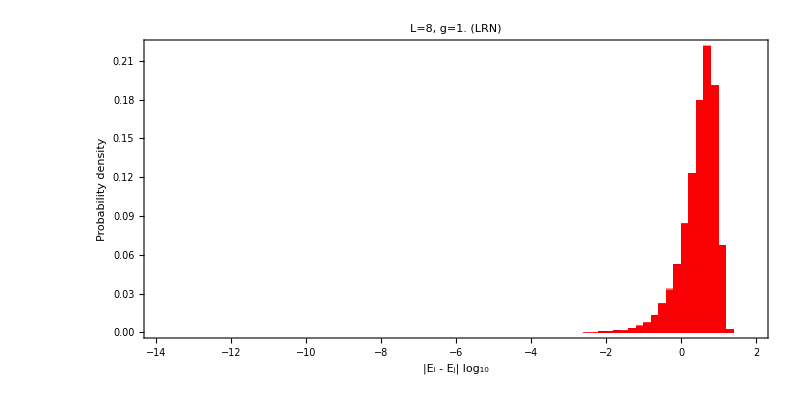

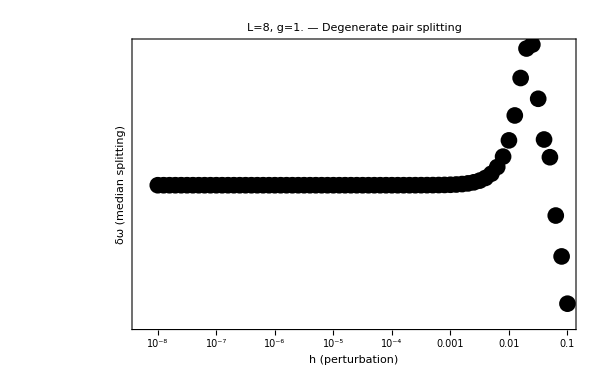

```mathematica
(* ============================================================*)(*PLOT 1:Log-gap histograms overlaid for each h*)(*x-axis=Log10(gap),y-axis=count*)(* ============================================================*)
logMin=Log10[Min[hScan]];logMax=Log10[Max[hScan]];
colors=Table[cf[Rescale[Log10[allResults[[i]]["h"]],{logMin,logMax},{0,1}]],{i,Length[allResults]}];
plotData=Table[Select[Log10[allResults[[i]]["allGaps"]],#>-15&],{i,Length[allResults]}];
plt1=Histogram[plotData,{0.2},(*bin width in decades*)"Probability",ChartStyle->(Directive[#,Opacity[0.4],EdgeForm[None]]&/@colors),PlotRange->{{-14,2},All},Frame->True,FrameLabel->{Style[Subscript["log","10"] Row[{"|",Subscript["E","i"]," - ",Subscript["E","j"],"|"}],14],Style["Probability density",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" (LRN)",14,Bold],ImageSize->800,AspectRatio->0.5]
(* ============================================================*)(*PLOT 2:Median splitting of degenerate pairs vs h*)(*This is the scalar that should track 1/T_M*)
splitData=Select[Table[{allResults[[i]]["h"],allResults[[i]]["medianSplit"]},{i,Length[allResults]}],#[[2]]>0&];
medianSplits=splitData;
plt2=ListLogLogPlot[medianSplits,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{Style["h (perturbation)",14],Style["δω (median splitting)",14]},FrameTicksStyle->12,PlotLabel->Style["L="<>ToString[LL]<>", g="<>ToString[gVal]<>" — Degenerate pair splitting",14],ImageSize->600,AspectRatio->0.65]
```